```mathematica
Import["/Users/wagner.palacio/Documents/Projeto/Repos/SystemModeling/Projects/Monkeypox/SEIQREpidemiologyModel.m"];
Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/Projects/Coronavirus-propagation-dynamics/WL/EpidemiologyModelModifications.m"];
Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/Projects/Coronavirus-propagation-dynamics/WL/EpidemiologyModelingVisualizationFunctions.m"];
Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/WL/SystemDynamicsInteractiveInterfacesFunctions.m"];
$PlotTheme = "Scientific";
```

```mathematica
cievsPEData := Import["https://raw.githubusercontent.com/palaciowagner/SystemModeling/master/Projects/Monkeypox/data/Pernambuco/Monkeypox%20-%20Pernambuco.csv", 
   "Dataset", "HeaderLines" -> 1];
owdPEData := Import["https://raw.githubusercontent.com/palaciowagner/SystemModeling/master/Projects/Monkeypox/data/OWD/latest_deprecated.csv", "Dataset", "HeaderLines" -> 1];
```

```mathematica
dateFormat = {"Day", "/", "Month", "/", "Year"};
PEdataMap = cievsPEData // Normal;
owdPEDataMap = Query[Select[StringContainsQ[ #Country, "Brazil"] && StringContainsQ[#Location, "Pernambuco"] && StringContainsQ[#Status, "confirmed"]&]] @ owdPEData;
```

```mathematica
pernambucoPopulation = QuantityMagnitude[9674793]; 
recifePopulation =  QuantityMagnitude[1661017]; 
maleInfected = 82.6/100;(*Cievs/PE. Dados atualizados em 10.11.2022, 15h.*)
estimatedInitialSusceptiblePopulation = ((recifePopulation/pernambucoPopulation)*maleInfected)*recifePopulation
```

235552.

```mathematica
groupedByDateOWD = GroupBy[Normal[owdPEDataMap], FromDateString[#"Date_confirmation", {"Year", "-", "Month", "-", "Day"}]&,Length] // Normal;
groupedCievs= Map[FromDateString[#Inicio, dateFormat]-> #"Confirmados" &,PEdataMap];
confirmadosJoined = Union[groupedByDateOWD, Take[groupedCievs, {15,-1}]] 
totalJoinedSmoothed = SmoothPeriod[Accumulate[TimeSeries[confirmadosJoined, TemporalRegularity->True]], 4, "Align"->Left];
(*SmoothPeriod[TimeSeries[Map[{FromDateString[#Inicio, dateFormat], #"Confirmados"} &,PEdataMap], TemporalRegularity -> True], 4, "Align"->Left]*)
(*totalConfirmadosOWDPE=Smooth[Accumulate[TimeSeries[groupedByDateOWD, TemporalRegularity->True]]];*)
totalConfirmadosPE = 
    SmoothPeriod[Accumulate[TimeSeries[Map[{FromDateString[#Inicio, dateFormat], #"Confirmados"} &,PEdataMap], TemporalRegularity -> True]], 4, "Align"->Left];
```

{Thu 21 Jul 2022→2,Fri 29 Jul 2022→4,Fri 5 Aug 2022→3,Sat 6 Aug 2022→3,Fri 12 Aug 2022→2,Tue 16 Aug 2022→1,Thu 18 Aug 2022→3,Wed 24 Aug 2022→4,Fri 26 Aug 2022→1,Mon 29 Aug 2022→1,Wed 31 Aug 2022→3,Thu 1 Sep 2022→14,Sun 4 Sep 2022→6,Tue 6 Sep 2022→1,Thu 8 Sep 2022→8,Fri 9 Sep 2022→4,Tue 13 Sep 2022→7,Wed 14 Sep 2022→23,Thu 15 Sep 2022→5,Fri 16 Sep 2022→12,Sat 17 Sep 2022→4,Tue 20 Sep 2022→7,Fri 23 Sep 2022→8,Tue 27 Sep 2022→2,Fri 30 Sep 2022→16,Tue 4 Oct 2022→10,Fri 7 Oct 2022→10,Tue 11 Oct 2022→0,Fri 14 Oct 2022→0,Tue 18 Oct 2022→1,Fri 21 Oct 2022→0,Tue 25 Oct 2022→3,Fri 28 Oct 2022→10,Tue 1 Nov 2022→8,Fri 4 Nov 2022→24,Tue 8 Nov 2022→3}

```mathematica
initialInfected =  Normal[totalJoinedSmoothed][[1]][[2]]
realIPData = <|"Infected"-> Ceiling[totalJoinedSmoothed["Values"]] // Normal|>
lsFocusParams = {β, α1, α2};
```

2

<|Infected→{2,6,6,11,12,14,17,18,23,24,34,48,58,84,105,122,127,136,154,164,164,164,165,167,173,186,210}|>

## Dados Literatura

Alguns dados que tirei de  artigos sobre a dinâmica da Monkeypox que serão uteis para as formulas

#### Periodo de Incubação

```mathematica
incubation = Range[5, 21];
incubationPeriod = Mean[incubation];
incubationPeriod
```

13

#### Período de Infecção [1]

```mathematica
prodomalPhase = Range[0, 3];
rashPhase = Range[7, 21];
infectiousPeriod = Mean[Map[Median] @ {prodomalPhase, rashPhase}]
maxInfectiousPeriod = Max[prodomalPhase, rashPhase]
medianInfectiousPeriod = Flatten[ {prodomalPhase,rashPhase}]
```

31/4

21

{0,1,2,3,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21}

#### Taxa de Recuperação (γ)

De acordo com [2], γ ==1/λ, sendo λ a média do período de infecção total.

## Otimização de parâmetros (β, α1, α2) dinâmico

```mathematica
(* Propagation Rate *)
ρt[t_, ζ_] := (NIP[t-5] +NIP[t-4]+ NIP[t-3])/(NIP[t-5-ζ] + NIP[t-4-ζ]+NIP[t-3-ζ])
(* Moving Average of Propagation Rate *)
ρT[T_,t_, ζ_]:=Sum[ρt[t+i, ζ],{i,-(T-1)/2,(T-1)/2}]*1/T
```

```mathematica
ClearAll[modelSEIQRDynamicBeta];
modelSEIQRDynamicBeta = With[{contactRate=ToExpression["Global`"<>"β"]},
model = SEIQRModel[t, "InitialConditions" -> True, "RateRules" -> True, 
   "TotalPopulationRepresentation" -> "Constant"];
(*lsRepRules={
contactRate -> contactRate[t]
};
(*model["Rates"] = KeyDrop[model["Rates"], {contactRate}];*)
model["Rates"]=KeyMap[#/. lsRepRules&,model["Rates"]];
model["Equations"]=Map[#/. lsRepRules&,model["Equations"]];
model["RateRules"]=Association[Normal[model["RateRules"]]/. lsRepRules];
model["RateRules"]=KeyDrop[model["RateRules"],{contactRate[t]}];*)
AppendTo[model["Stocks"],NIP[t]->"Newly Infected Population"];
AppendTo[model["Stocks"],PR[t]->"Propagation Rate"];model["InitialConditions"]=ReplacePart[model["InitialConditions"],3-> IP[t /; t<=0]==initialInfected];
(*AppendTo[modelSEIQRDynamicBeta["InitialConditions"], NIP[t/; IP[-1+t]+IP[t]===0]==1];*)
AppendTo[model["InitialConditions"], NIP[t /; t<=0]==1];
AppendTo[model["InitialConditions"], PR[t /; t<=0]==0];
AppendTo[model["Equations"], NIP'[t]==IP[t]-IP[t-1]];
AppendTo[model["Equations"], PR'[t]==ρT[7,t, ζ] ];
(*AppendTo[model["Equations"], ρ'[T]==((ρ[t-6] + ρ[t-5] +ρ[t-4] + ρ[t-3]+ ρ[t-2]+ρ[t])/T ];*)

(*AppendTo[model["InitialConditions"],  β[t /; t<=0]==0.001];*)
model];
```

```mathematica
modelSEIQRDynamicBeta = SetRateRules[modelSEIQRDynamicBeta, 
<|NP[0] -> Round[estimatedInitialSusceptiblePopulation/100],
λ-> infectiousPeriod,
ζ->incubationPeriod|>
];
modelSEIQRDynamicBeta = SetInitialConditions[modelSEIQRDynamicBeta,
   <|
SP[0] ->  Round[estimatedInitialSusceptiblePopulation/100],
EP[0] -> 2,
QP[0] -> 8
    |>];
```

```mathematica
lsActualEquationsDynamicBeta = Join[modelSEIQRDynamicBeta["Equations"]//.KeyDrop[modelSEIQRDynamicBeta["RateRules"], lsFocusParams],modelSEIQRDynamicBeta["InitialConditions"]]
ModelGridTableForm[modelSEIQRDynamicBeta]
```

{SP'[t]==0.2 QP[t]-(β IP[t] SP[t])/2356,EP'[t]==-((α1+α2) EP[t])+(β IP[t] SP[t])/2356,IP'[t]==α1 EP[t]-(4 IP[t])/31,QP'[t]==α2 EP[t]-0.329032 QP[t],RP'[t]==(4 IP[t])/31+(4 QP[t])/31,NIP'[t]==-IP[-1+t]+IP[t],PR'[t]==1/7 ((NIP[-8+t]+NIP[-7+t]+NIP[-6+t])/(NIP[-21+t]+NIP[-20+t]+NIP[-19+t])+(NIP[-7+t]+NIP[-6+t]+NIP[-5+t])/(NIP[-20+t]+NIP[-19+t]+NIP[-18+t])+(NIP[-6+t]+NIP[-5+t]+NIP[-4+t])/(NIP[-19+t]+NIP[-18+t]+NIP[-17+t])+(NIP[-5+t]+NIP[-4+t]+NIP[-3+t])/(NIP[-18+t]+NIP[-17+t]+NIP[-16+t])+(NIP[-4+t]+NIP[-3+t]+NIP[-2+t])/(NIP[-17+t]+NIP[-16+t]+NIP[-15+t])+(NIP[-3+t]+NIP[-2+t]+NIP[-1+t])/(NIP[-16+t]+NIP[-15+t]+NIP[-14+t])+(NIP[-2+t]+NIP[-1+t]+NIP[t])/(NIP[-15+t]+NIP[-14+t]+NIP[-13+t])),SP[0]==2356,EP[0]==2,IP[t/;t≤0]==2,QP[0]==8,RP[0]==0,NIP[t/;t≤0]==1,PR[t/;t≤0]==0}

<|Stocks→# | Symbol | Description
1 | NP[t] | Total Population
2 | SP[t] | Susceptible Population
3 | EP[t] | Exposed Population
4 | IP[t] | Infected Population
5 | QP[t] | Quarantined Population
6 | RP[t] | Recovered Population
7 | NIP[t] | Newly Infected Population
8 | PR[t] | Propagation Rate,Rates→# | Symbol | Description
1 | β | Contact rate for the infected population
2 | α1 | Proportion of Exposed to Infected Rate (Confirmed)
3 | α2 | Proportion Sent to Quarantine (Suspected)
4 | φ | Proportion of not detected after medical diagnosis (Discarded)
5 | τ | Proportion from Suspected to Recovered class
6 | γ | Recovery Rate
7 | ζ | Average Incubation Period
8 | λ | Average Infection Period,Equations→# | Equation
1 | SP'[t]==φ QP[t]-(β IP[t] SP[t])/NP[0]
2 | EP'[t]==-((α1+α2) EP[t])+(β IP[t] SP[t])/NP[0]
3 | IP'[t]==α1 EP[t]-γ IP[t]
4 | QP'[t]==α2 EP[t]-(τ+φ) QP[t]
5 | RP'[t]==γ IP[t]+τ QP[t]
6 | NIP'[t]==-IP[-1+t]+IP[t]
7 | PR'[t]==1/7 ((NIP[-8+t]+NIP[-7+t]+NIP[-6+t])/(NIP[-8+t-ζ]+NIP[-7+t-ζ]+NIP[-6+t-ζ])+(NIP[-7+t]+NIP[-6+t]+NIP[-5+t])/(NIP[-7+t-ζ]+NIP[-6+t-ζ]+NIP[-5+t-ζ])+(NIP[-6+t]+NIP[-5+t]+NIP[-4+t])/(NIP[-6+t-ζ]+NIP[-5+t-ζ]+NIP[-4+t-ζ])+(NIP[-5+t]+NIP[-4+t]+NIP[-3+t])/(NIP[-5+t-ζ]+NIP[-4+t-ζ]+NIP[-3+t-ζ])+(NIP[-4+t]+NIP[-3+t]+NIP[-2+t])/(NIP[-4+t-ζ]+NIP[-3+t-ζ]+NIP[-2+t-ζ])+(NIP[-3+t]+NIP[-2+t]+NIP[-1+t])/(NIP[-3+t-ζ]+NIP[-2+t-ζ]+NIP[-1+t-ζ])+(NIP[-2+t]+NIP[-1+t]+NIP[t])/(NIP[-2+t-ζ]+NIP[-1+t-ζ]+NIP[t-ζ])),RateRules→# | Symbol | Value
1 | NP[0] | 2356
2 | β | 6.×10^-6
3 | α1 | 1/ζ
4 | α2 | 1/ζ
5 | φ | 0.2
6 | τ | γ
7 | γ | 1/λ
8 | ζ | 13
9 | λ | 31/4,InitialConditions→# | Equation
1 | SP[0]==2356
2 | EP[0]==2
3 | IP[t/;t≤0]==2
4 | QP[0]==8
5 | RP[0]==0
6 | NIP[t/;t≤0]==1
7 | PR[t/;t≤0]==0|>

```mathematica
asolDynamicBeta = Association @ Flatten@ParametricNDSolve[lsActualEquationsDynamicBeta,{SP,EP,IP,QP, RP, NIP, PR},{t,0,100},lsFocusParams, Method->Automatic,MaxStepSize->1, StartingStepSize->1]
```

<|SP→ParametricFunction[<>],EP→ParametricFunction[<>],IP→ParametricFunction[<>],QP→ParametricFunction[<>],RP→ParametricFunction[<>],NIP→ParametricFunction[<>],PR→ParametricFunction[<>]|>

```mathematica
ResourceFunction["GridTableForm"][List /@ lsActualEquationsDynamicBeta]
```

# | 1
1 | SP'[t]==0.2 QP[t]-(β IP[t] SP[t])/2356
2 | EP'[t]==-((α1+α2) EP[t])+(β IP[t] SP[t])/2356
3 | IP'[t]==α1 EP[t]-(4 IP[t])/31
4 | QP'[t]==α2 EP[t]-0.329032 QP[t]
5 | RP'[t]==(4 IP[t])/31+(4 QP[t])/31
6 | NIP'[t]==-IP[-1+t]+IP[t]
7 | PR'[t]==1/7 ((NIP[-8+t]+NIP[-7+t]+NIP[-6+t])/(NIP[-21+t]+NIP[-20+t]+NIP[-19+t])+(NIP[-7+t]+NIP[-6+t]+NIP[-5+t])/(NIP[-20+t]+NIP[-19+t]+NIP[-18+t])+(NIP[-6+t]+NIP[-5+t]+NIP[-4+t])/(NIP[-19+t]+NIP[-18+t]+NIP[-17+t])+(NIP[-5+t]+NIP[-4+t]+NIP[-3+t])/(NIP[-18+t]+NIP[-17+t]+NIP[-16+t])+(NIP[-4+t]+NIP[-3+t]+NIP[-2+t])/(NIP[-17+t]+NIP[-16+t]+NIP[-15+t])+(NIP[-3+t]+NIP[-2+t]+NIP[-1+t])/(NIP[-16+t]+NIP[-15+t]+NIP[-14+t])+(NIP[-2+t]+NIP[-1+t]+NIP[t])/(NIP[-15+t]+NIP[-14+t]+NIP[-13+t]))
8 | SP[0]==2356
9 | EP[0]==2
10 | IP[t/;t≤0]==2
11 | QP[0]==8
12 | RP[0]==0
13 | NIP[t/;t≤0]==1
14 | PR[t/;t≤0]==0

```mathematica
allValues =Map[ParametricFunctionValues[#,<|β->0.517,α1->0.729,α2->0.692|>, {0,21,1}]&, asolDynamicBeta]
```

ParametricNDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

General::stop: Further output of ParametricNDSolve::ihist will be suppressed during this calculation.

<|SP→{{21,2269.63},{22,2258.04},{23,2245.2},{24,2231.02},{25,2215.39},{26,2198.19},{27,2179.32},{28,2158.66},{29,2136.11},{30,2111.58},{31,2084.99},{32,2056.28},{33,2025.38},{34,1992.3},{35,1957.02},{36,1919.59},{37,1880.09},{38,1838.63},{39,1795.35},{40,1750.44},{41,1704.11},{42,1656.63}},EP→{{21,9.10868},{22,10.1094},{23,11.2031},{24,12.3942},{25,13.6865},{26,15.0827},{27,16.584},{28,18.1898},{29,19.8975},{30,21.7018},{31,23.5943},{32,25.5635},{33,27.5943},{34,29.6679},{35,31.7616},{36,33.8495},{37,35.9024},{38,37.8887},{39,39.7754},{40,41.5288},{41,43.1164},{42,44.5075}},IP→{{21,27.9078},{22,31.1035},{23,34.629},{24,38.5095},{25,42.77},{26,47.4348},{27,52.5265},{28,58.0652},{29,64.0675},{30,70.5453},{31,77.5043},{32,84.9427},{33,92.85},{34,101.205},{35,109.975},{36,119.115},{37,128.567},{38,138.256},{39,148.099},{40,157.995},{41,167.837},{42,177.506}},QP→{{21,14.4475},{22,16.0747},{23,17.8644},{24,19.8273},{25,21.9735},{26,24.3122},{27,26.8512},{28,29.5962},{29,32.5503},{30,35.7135},{31,39.0817},{32,42.6459},{33,46.3921},{34,50.2997},{35,54.3419},{36,58.4849},{37,62.6881},{38,66.9042},{39,71.0802},{40,75.158},{41,79.0765},{42,82.7727}},RP→{{21,46.9054},{22,52.6767},{23,59.1016},{24,66.2461},{25,74.1805},{26,82.9797},{27,92.7228},{28,103.492},{29,115.374},{30,128.456},{31,142.825},{32,158.571},{33,175.779},{34,194.531},{35,214.901},{36,236.956},{37,260.749},{38,286.323},{39,313.699},{40,342.883},{41,373.858},{42,406.585}},NIP→{{21,25.4379},{22,28.4792},{23,31.8377},{24,35.5386},{25,39.6071},{26,44.0678},{27,48.9442},{28,54.2579},{29,60.0272},{30,66.2665},{31,72.9846},{32,80.1838},{33,87.858},{34,95.9914},{35,104.557},{36,113.517},{37,122.818},{38,132.395},{39,142.169},{40,152.047},{41,161.925},{42,171.691}},PR→{{21,89.6281},{22,95.3704},{23,100.815},{24,106.068},{25,111.171},{26,116.143},{27,120.997},{28,125.743},{29,130.387},{30,134.936},{31,139.391},{32,143.756},{33,148.032},{34,152.217},{35,156.311},{36,160.312},{37,164.218},{38,168.026},{39,171.732},{40,175.335},{41,178.83},{42,182.213}}|>

```mathematica
(*positions = Flatten@Values@ PositionIndex @ Keys[ modelSEIQRDynamicBeta["Stocks"]];
First@positions*)
```

```mathematica
(*({#[20]})& /@ asolDynamicBeta *)
```

```mathematica
opts={PlotRange->All,PlotLegends->None,PlotTheme->"Detailed",PerformanceGoal->"Speed",ImageSize->800};
Manipulate[
DynamicModule[{lsPopulationPlots2},
lsPopulationPlots2=
Quiet[ParametricSolutionsPlots[
modelSEIQRDynamicBeta["Stocks"],
KeyTake[asolDynamicBeta,GetPopulationSymbols[modelSEIQRDynamicBeta, __ ~~ "Population"]],{contactRate, alpha1, alpha2},nWeeks,"Together"->popTogetherQ,opts]];
  Show[lsPopulationPlots2[[3]],ListPlot[PadRealData[realIPData,Round[incubationPeriod+padOffset],Round[infectionPeriod+padOffset]],PlotStyle->{Blue,Black,Red}]]
  (*Multicolumn[plots, nPlotColumns, Dividers -> All, 
   FrameStyle -> GrayLevel[0.8]]*)
],
{{population,estimatedInitialSusceptiblePopulation/100,"Population"},100,estimatedInitialSusceptiblePopulation,50,Appearance->{"Open"}},
{{padOffset,0,"real data padding offset"},-100,100,1,Appearance->{"Open"}},
{{contactRate, 0.540, StringJoin["Contact rate of the infected population (β)", ToString[DisplayForm[InterpretationBox[SuperscriptBox["10", "-4"], var]]]]}, 0.001, 1, 0.001, 
  Appearance -> {"Open"}},
 {{incubationPeriod, 13, "Incubation period (ζ) in days "}, 5, 21, 1, 
  Appearance -> {"Open"}},
 {{alpha1, 0.718, "Alpha 1(α1)"}, 0, 1, 0.001, 
  Appearance -> {"Open"}},
 {{alpha2, 0.693, "Alpha 2(α2)"}, 0, 1, 0.001, 
  Appearance -> {"Open"}},
 {{infectionPeriod,7, "Infection period (λ) in days "}, 0, 21, 1, 
  Appearance -> {"Open"}},
 {{nWeeks,28, "Epidemiological Week (t)"}, 1, 52, 1, Appearance -> {"Open"}},
 {{nPlotColumns, 1, "Number of plot columns"}, Range[3]}, 
{{popTogetherQ, False, "Plot populations together"}, {False, True}},
ControlPlacement->Left,ContinuousAction->False]
```

```mathematica
totalNewlyInfectedOptimizedDynamic = SmoothPeriod[Accumulate[TimeSeries[confirmadosJoined, TemporalRegularity->True]],7, "Align"-> Left] // Normal
```

{{Thu 21 Jul 2022 00:00:00GMT-3,2},{Thu 28 Jul 2022 00:00:00GMT-3,6},{Thu 4 Aug 2022 00:00:00GMT-3,11},{Thu 11 Aug 2022 00:00:00GMT-3,16},{Thu 18 Aug 2022 00:00:00GMT-3,20},{Thu 25 Aug 2022 00:00:00GMT-3,29},{Thu 1 Sep 2022 00:00:00GMT-3,48},{Thu 8 Sep 2022 00:00:00GMT-3,74},{Thu 15 Sep 2022 00:00:00GMT-3,108},{Thu 22 Sep 2022 00:00:00GMT-3,127},{Thu 29 Sep 2022 00:00:00GMT-3,149},{Thu 6 Oct 2022 00:00:00GMT-3,164},{Thu 13 Oct 2022 00:00:00GMT-3,165},{Thu 20 Oct 2022 00:00:00GMT-3,167},{Thu 27 Oct 2022 00:00:00GMT-3,182}}

```mathematica
(*totalSusceptibleOptimized = SmoothPeriod[Accumulate[TimeSeries[expostosJoined, TemporalRegularity->True]],maxInfectiousPeriod] // Normal*)
firstDateInfectedDynamic = First @ First@Normal[totalNewlyInfectedOptimizedDynamic];
lastDateInfectedDynamic = First @  Last@ Normal[totalNewlyInfectedOptimizedDynamic];
fitInfectedDataDynamic={ToModelTime[firstDateInfectedDynamic, #1], #2}& @@@ Normal[totalNewlyInfectedOptimizedDynamic] //Echo[#, "", Multicolumn]&;
```

{0,2} | {28,20} | {56,108} | {84,165}
{7,6} | {35,29} | {63,127} | {91,167}
{14,11} | {42,48} | {70,149} | {98,182}
{21,16} | {49,74} | {77,164} |

```mathematica
newlyInfectedSol =  Association@Flatten@Quiet[ParametricNDSolve[lsActualEquationsDynamicBeta,{SP,EP,IP,QP, RP, NIP,PR},{t,0,99},lsFocusParams,MaxStepSize->1, StartingStepSize->1]];
{infectedSolDynamic, betaSolDynamic}= {IP[β,α1,α2], PR[β,α1,α2]} /.newlyInfectedSol;
currentDynamic = Take[totalNewlyInfectedOptimizedDynamic,15]
```

{{Thu 21 Jul 2022 00:00:00GMT-3,2},{Thu 28 Jul 2022 00:00:00GMT-3,6},{Thu 4 Aug 2022 00:00:00GMT-3,11},{Thu 11 Aug 2022 00:00:00GMT-3,16},{Thu 18 Aug 2022 00:00:00GMT-3,20},{Thu 25 Aug 2022 00:00:00GMT-3,29},{Thu 1 Sep 2022 00:00:00GMT-3,48},{Thu 8 Sep 2022 00:00:00GMT-3,74},{Thu 15 Sep 2022 00:00:00GMT-3,108},{Thu 22 Sep 2022 00:00:00GMT-3,127},{Thu 29 Sep 2022 00:00:00GMT-3,149},{Thu 6 Oct 2022 00:00:00GMT-3,164},{Thu 13 Oct 2022 00:00:00GMT-3,165},{Thu 20 Oct 2022 00:00:00GMT-3,167},{Thu 27 Oct 2022 00:00:00GMT-3,182}}

```mathematica
all = {ToModelTime[First@First@Normal[currentDynamic], #1], #2}& @@@ Normal[currentDynamic]
s01 = Take[all,4]
s02=Take[all,{5,8}]
s03=Take[all,{9,12}]
s04=Take[all,-3]
```

{{0,2},{7,6},{14,11},{21,16},{28,20},{35,29},{42,48},{49,74},{56,108},{63,127},{70,149},{77,164},{84,165},{91,167},{98,182}}

{{0,2},{7,6},{14,11},{21,16}}

{{28,20},{35,29},{42,48},{49,74}}

{{56,108},{63,127},{70,149},{77,164}}

```mathematica
(*{{β,0.517}, {α1,0.729},{α2,0.692}*)
```

```mathematica
(*GetFittingModelFor := Block[{data, beta, alpha1, alpha2},*)AbsoluteTiming[fitInfectedDynamic=NonlinearModelFit[s01,{infectedSolDynamic[t], {0<β && 0<α1<=1 && 0< α2<=1}},{{β,0.517}, {α1,0.729},{α2,0.692}},t, AccuracyGoal-> 3, WorkingPrecision-> 3,  PrecisionGoal -> 3, EvaluationMonitor:> Print["β=", β,"  .α1=",α1,"   .α2=",α2],Method-> {NMinimize, Method->{"NelderMead", "PostProcess"-> {"FindMinimum"}}}]]
(*fitInfectedDynamic=NonlinearModelFit[{ToModelTime[First@First@Normal[currentDynamic], #1], #2}& @@@ Normal[currentDynamic],{infectedSolDynamic[t], α1>0&&α2 >0&&β>0},{{β,2.5},{α1,0.03},{α2,0.02}},t, AccuracyGoal-> 3, WorkingPrecision-> 6,  PrecisionGoal -> 3, EvaluationMonitor:>Print["t=", t, ".    β=", β, ".    α1=", α1, ".    α2=", α2], Method->  {NMinimize,Method->{"DifferentialEvolution","ScalingFactor"->0.9,"CrossProbability"->0.1,"PostProcess"->{FindMinimum,Method->"QuasiNewton"}}}]*)
(*GetFittingModelFor[s01,0.517,0.729,  0.692]*)
```

ParametricNDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

General::stop: Further output of ParametricNDSolve::ihist will be suppressed during this calculation.

β=0.517  .α1=0.729   .α2=0.692

β=1.07973  .α1=0.833591   .α2=0.826558

β=0.627259  .α1=0.880957   .α2=0.420882

β=1.3341  .α1=0.327687   .α2=0.727544

β=0.572514  .α1=0.458171   .α2=0.400393

β=0.988487  .α1=0.128949   .α2=0.79241

ParametricNDSolve::ndsz: At t == 25.6138, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolve::ndsz will be suppressed during this calculation.

β=0.051229  .α1=0.549727   .α2=0.528991

β=0.465297  .α1=0.480279   .α2=0.941874

β=1.26263  .α1=0.342425   .α2=0.957619

β=0.354078  .α1=0.497901   .α2=0.668876

β=0.00943698  .α1=0.969738   .α2=0.742757

β=0.716973  .α1=0.349004   .α2=0.779996

β=0.778768  .α1=0.540954   .α2=0.940371

β=0.460251  .α1=0.508664   .α2=0.73675

β=0.664185  .α1=0.5775   .α2=0.530624

β=0.515019  .α1=0.504584   .α2=0.839061

β=0.611162  .α1=0.179169   .α2=0.878538

β=0.54054  .α1=0.591542   .α2=0.738635

β=0.721437  .α1=0.454756   .α2=0.835045

β=0.804281  .α1=0.425617   .α2=0.730056

β=0.587335  .α1=0.484842   .α2=0.81181

β=0.515902  .α1=0.671756   .α2=0.81033

β=0.415367  .α1=0.833132   .α2=0.825497

β=0.597919  .α1=0.660527   .α2=0.77753

β=0.589981  .α1=0.528764   .α2=0.80324

β=0.376178  .α1=0.739952   .α2=0.733091

β=0.635122  .α1=0.526055   .α2=0.809557

β=0.462493  .α1=0.668653   .α2=0.75858

β=0.591965  .α1=0.561704   .α2=0.796812

β=0.50565  .α1=0.633003   .α2=0.771324

β=0.570386  .α1=0.579529   .α2=0.79044

β=0.494572  .α1=0.699788   .α2=0.756363

β=0.463623  .α1=0.729195   .α2=0.746445

β=0.442191  .α1=0.808951   .α2=0.803458

β=0.515953  .α1=0.645894   .α2=0.75484

β=0.502414  .α1=0.664776   .α2=0.784714

β=0.496532  .α1=0.691035   .α2=0.763451

β=0.555302  .α1=0.609929   .α2=0.805969

β=0.486543  .α1=0.699378   .α2=0.761326

β=0.483365  .α1=0.728885   .α2=0.801898

β=0.491512  .α1=0.708138   .α2=0.790133

β=0.467156  .α1=0.727278   .α2=0.732943

β=0.442783  .α1=0.755039   .α2=0.69425

β=0.450693  .α1=0.750668   .α2=0.733689

β=0.485073  .α1=0.705943   .α2=0.75601

β=0.45142  .α1=0.732103   .α2=0.684258

β=0.431375  .α1=0.744085   .α2=0.63132

β=0.419611  .α1=0.770666   .α2=0.626394

β=0.386145  .α1=0.80631   .α2=0.558928

β=0.37744  .α1=0.80725   .α2=0.545299

β=0.458164  .α1=0.73127   .α2=0.703333

β=0.429983  .α1=0.742309   .α2=0.613114

β=0.439583  .α1=0.751856   .α2=0.673966

β=0.402215  .α1=0.779802   .α2=0.584454

β=0.395883  .α1=0.777846   .α2=0.554146

β=0.374033  .α1=0.790841   .α2=0.494236

β=0.365865  .α1=0.816787   .α2=0.505403

β=0.414997  .α1=0.762261   .α2=0.599841

β=0.403546  .α1=0.769377   .α2=0.562526

β=0.37544  .α1=0.777652   .α2=0.478008

β=0.353355  .α1=0.781146   .α2=0.403815

β=0.338959  .α1=0.798648   .α2=0.373877

β=0.30094  .α1=0.816842   .α2=0.260896

β=0.282006  .α1=0.823175   .α2=0.210105

β=0.373161  .α1=0.782826   .α2=0.474421

β=0.310938  .α1=0.796368   .α2=0.265185

β=0.270327  .α1=0.813411   .α2=0.145509

β=0.21891  .α1=0.828703   .α2=0.0000796861

β=0.234782  .α1=0.836601   .α2=0.0439116

β=0.323712  .α1=0.795009   .α2=0.313839

β=0.285715  .α1=0.820473   .α2=0.214978

β=0.304632  .α1=0.802394   .α2=0.252633

β=0.260221  .α1=0.826755   .α2=0.12552

β=0.307839  .α1=0.802946   .α2=0.266759

β=0.287592  .α1=0.795659   .α2=0.182372

β=0.297603  .α1=0.811546   .α2=0.241265

β=0.279214  .α1=0.816207   .α2=0.183056

β=0.256924  .α1=0.824497   .α2=0.113127

β=0.29511  .α1=0.808334   .α2=0.228351

β=0.296146  .α1=0.805986   .α2=0.227028

β=0.276786  .α1=0.806941   .α2=0.159327

β=0.265336  .α1=0.813137   .α2=0.128431

β=0.249931  .α1=0.816713   .α2=0.0791321

β=0.246523  .α1=0.813992   .α2=0.0604935

β=0.222229  .α1=0.816822   .α2=2.90346×10^-7

β=0.244672  .α1=0.820086   .α2=0.0636283

β=0.268757  .α1=0.810227   .α2=0.135402

β=0.250084  .α1=0.811494   .α2=0.0707087

β=0.244906  .α1=0.810672   .α2=0.0493058

β=0.234691  .α1=0.809439   .α2=0.00974346

β=0.218774  .α1=0.813056   .α2=3.61089×10^-7

β=0.256262  .α1=0.810934   .α2=0.0911922

β=0.23127  .α1=0.812349   .α2=0.00277159

β=0.218774  .α1=0.813056   .α2=2.94763×10^-7

β=0.224906  .α1=0.81236   .α2=1.91028×10^-7

β=0.243789  .α1=0.81171   .α2=0.0475224

β=0.226644  .α1=0.80834   .α2=7.48051×10^-7

β=0.241553  .α1=0.812579   .α2=0.040253

β=0.227887  .α1=0.811201   .α2=5.49756×10^-7

β=0.239814  .α1=0.811583   .α2=0.0325559

β=0.228964  .α1=0.809668   .α2=7.45998×10^-7

β=0.238406  .α1=0.811851   .α2=0.0276383

β=0.238302  .α1=0.814417   .α2=0.0322338

β=0.235594  .α1=0.810683   .α2=0.015366

β=0.230366  .α1=0.811673   .α2=4.90767×10^-7

β=0.225642  .α1=0.811718   .α2=4.92705×10^-7

β=0.226414  .α1=0.811285   .α2=5.29266×10^-7

β=0.235408  .α1=0.81171   .α2=0.0168422

β=0.229102  .α1=0.813138   .α2=3.49662×10^-7

β=0.233971  .α1=0.811297   .α2=0.0109521

β=0.22833  .α1=0.811836   .α2=5.15445×10^-8

β=0.233639  .α1=0.811741   .α2=0.0107085

β=0.229546  .α1=0.812545   .α2=3.41863×10^-8

β=0.230652  .α1=0.812233   .α2=0.00224677

β=0.227887  .α1=0.812428   .α2=3.10268×10^-8

β=0.232201  .α1=0.811913   .α2=0.0061907

β=0.229325  .α1=0.812257   .α2=4.48292×10^-8

β=0.231482  .α1=0.811999   .α2=0.00393183

β=0.231427  .α1=0.811781   .α2=0.0022225

β=0.23056  .α1=0.811869   .α2=4.48968×10^-8

β=0.2301  .α1=0.811804   .α2=1.77161×10^-8

β=0.230038  .α1=0.812147   .α2=4.56562×10^-8

β=0.230385  .α1=0.812055   .α2=0.000462044

β=0.229604  .α1=0.811382   .α2=8.20781×10^-8

β=0.230854  .α1=0.812107   .α2=0.00146289

β=0.230021  .α1=0.811624   .α2=1.99451×10^-8

β=0.230645  .α1=0.811986   .α2=0.000808543

β=0.230663  .α1=0.811631   .α2=0.0000773417

β=0.23056  .α1=0.811869   .α2=4.48968×10^-8

β=0.23056  .α1=0.811869   .α2=4.48968×10^-8

β=0.23056  .α1=0.811869   .α2=4.48968×10^-8

β=0.23056  .α1=0.811869   .α2=5.9798×10^-8

β=0.23056  .α1=0.811869   .α2=4.48968×10^-8

β=0.23056  .α1=0.811869   .α2=4.48968×10^-8

β=0.23056  .α1=0.811869   .α2=4.48968×10^-8

«2 more identical outputs»

β=0.23056  .α1=0.811869   .α2=5.9798×10^-8

β=0.23056  .α1=0.811869   .α2=4.48968×10^-8

β=-0.230467  .α1=0.9622   .α2=-0.121879

β=-0.230467  .α1=0.9622   .α2=-0.121879

β=-0.230467  .α1=0.9622   .α2=-0.121879

«2 more identical outputs»

β=0.23056  .α1=0.811869   .α2=4.48968×10^-8

β=0.23056  .α1=0.811869   .α2=4.48968×10^-8

β=0.23056  .α1=0.811869   .α2=4.48968×10^-8

ParametricNDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

{203.266,FittedModel[InterpolatingFunction[…][t]]}

| Estimate | Standard Error | t-Statistic | P-Value
β | 0.231 | 20.439 | 0.0112804 | 0.992819
α1 | 0.812 | 102.15 | 0.00794778 | 0.99494
α2 | 4.49×10^-8 | 88.5169 | 5.07212×10^-10 | 1

{β→0.231,α1→0.812,α2→4.49×10^-8}

0.993245

0.97298

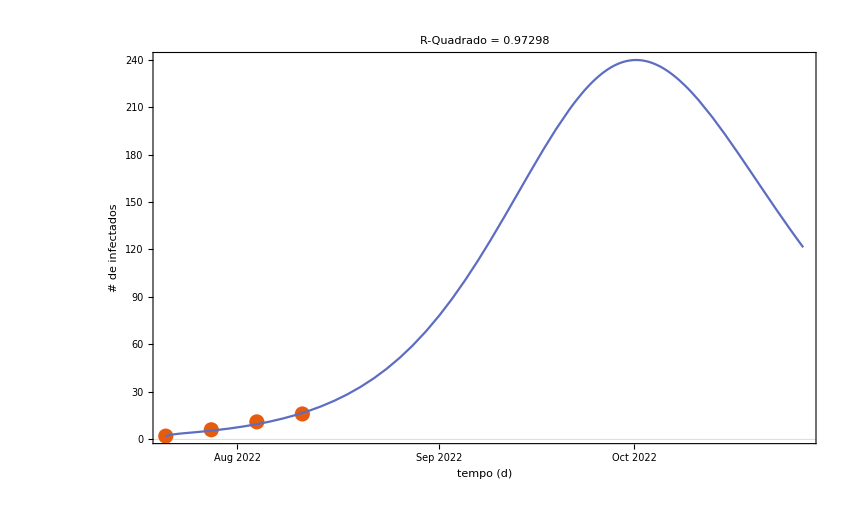

```mathematica
Quiet @ fitInfectedDynamic["ParameterTable"]
Quiet @ fitInfectedDynamic["BestFitParameters"]
Quiet @fitInfectedDynamic["RSquared"]
Quiet @fitInfectedDynamic["AdjustedRSquared"]
Quiet @FitWithDataPlot[fitInfectedDynamic,{First@First@Normal[currentDynamic],First@Last@Normal[currentDynamic]} ]
```

### Simulação 2

```mathematica
resultsS01 =Map[ParametricFunctionValues[#,<|β->0.231,α1->0.812,α2->N[4.49*10^-8]|>, {0,21,1}]&, asolDynamicBeta];
s01AsMap = Map[Last[Last[Last[#]]]&,Normal@resultsS01]
```

ParametricNDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

General::stop: Further output of ParametricNDSolve::ihist will be suppressed during this calculation.

{2322.02,4.28012,16.7233,0.00798511,24.9642,15.0808,75.0995}

```mathematica
Total[Take[s01AsMap,5]]
```

2368.

```mathematica
(*modelSEIQRDynamicBetaS02 = SetRateRules[modelSEIQRDynamicBetaS02, <|NP[0] -> N[Total[Take[s01AsMap,5]]] |>];
modelSEIQRDynamicBetaS02 = SetInitialConditions[modelSEIQRDynamicBetaS02,
   <|
SP[21] ->  First@s01AsMap,
EP[21] -> s01AsMap[[2]],
IP[21] ->s01AsMap[[3]],
QP[21] ->s01AsMap[[4]],
RP[21] ->s01AsMap[[5]],
NIP[21] ->s01AsMap[[6]],
PR[21] ->s01AsMap[[7]],
    |>]*)
```

Part::partd: Part specification Null⟦1⟧ is longer than depth of object.

<|Stocks→<|NP[t]→Total Population,SP[t]→Susceptible Population,EP[t]→Exposed Population,IP[t]→Infected Population,QP[t]→Quarantined Population,RP[t]→Recovered Population,NIP[t]→Newly Infected Population,PR[t]→Propagation Rate|>,Rates→<|β→Contact rate for the infected population,α1→Proportion of Exposed to Infected Rate (Confirmed),α2→Proportion Sent to Quarantine (Suspected),φ→Proportion of not detected after medical diagnosis (Discarded),τ→Proportion from Suspected to Recovered class,γ→Recovery Rate,ζ→Average Incubation Period,λ→Average Infection Period|>,Equations→{SP'[t]==φ QP[t]-(β IP[t] SP[t])/NP[0],EP'[t]==-((α1+α2) EP[t])+(β IP[t] SP[t])/NP[0],IP'[t]==α1 EP[t]-γ IP[t],QP'[t]==α2 EP[t]-(τ+φ) QP[t],RP'[t]==γ IP[t]+τ QP[t],NIP'[t]==-IP[-1+t]+IP[t],PR'[t]==1/7 ((NIP[-8+t]+NIP[-7+t]+NIP[-6+t])/(NIP[-8+t-ζ]+NIP[-7+t-ζ]+NIP[-6+t-ζ])+(NIP[-7+t]+NIP[-6+t]+NIP[-5+t])/(NIP[-7+t-ζ]+NIP[-6+t-ζ]+NIP[-5+t-ζ])+(NIP[-6+t]+NIP[-5+t]+NIP[-4+t])/(NIP[-6+t-ζ]+NIP[-5+t-ζ]+NIP[-4+t-ζ])+(NIP[-5+t]+NIP[-4+t]+NIP[-3+t])/(NIP[-5+t-ζ]+NIP[-4+t-ζ]+NIP[-3+t-ζ])+(NIP[-4+t]+NIP[-3+t]+NIP[-2+t])/(NIP[-4+t-ζ]+NIP[-3+t-ζ]+NIP[-2+t-ζ])+(NIP[-3+t]+NIP[-2+t]+NIP[-1+t])/(NIP[-3+t-ζ]+NIP[-2+t-ζ]+NIP[-1+t-ζ])+(NIP[-2+t]+NIP[-1+t]+NIP[t])/(NIP[-2+t-ζ]+NIP[-1+t-ζ]+NIP[t-ζ]))},RateRules→<|NP[0]→2368.,β→6.×10^-6,α1→1/ζ,α2→1/ζ,φ→0.2,τ→γ,γ→1/λ,ζ→13,λ→31/4|>,InitialConditions→{SP[0]==2322.02,EP[0]==4.28012,IP[t/;t≤0]==2,QP[0]==0.00798511,RP[0]==24.9642,NIP[t/;t≤0]==1,PR[t/;t≤0]==0}|>

```mathematica
AbsoluteTiming[fitInfectedDynamic02=NonlinearModelFit[s02,{infectedSolDynamic[t], {0<β && 0<α1<=1 && 0< α2<=1}},{{β,0.231}, {α1,0.812},{α2,N[4.49*10^-8]}},t, AccuracyGoal-> 3, WorkingPrecision-> 3,  PrecisionGoal -> 3, EvaluationMonitor:> Print["β=", β,"  .α1=",α1,"   .α2=",α2],Method-> {NMinimize, Method->{"NelderMead", "PostProcess"-> {"FindMinimum"}}}]]
```

ParametricNDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

General::stop: Further output of ParametricNDSolve::ihist will be suppressed during this calculation.

β=0.231  .α1=0.812   .α2=4.49×10^-8

β=1.07973  .α1=0.833591   .α2=0.826558

β=0.627259  .α1=0.880957   .α2=0.420882

β=1.3341  .α1=0.327687   .α2=0.727544

β=1.13596  .α1=0.434562   .α2=0.615186

β=0.720983  .α1=0.215908   .α2=0.0685958

β=0.990042  .α1=0.67917   .α2=0.637067

β=0.231  .α1=0.812   .α2=4.49×10^-8

β=0.655364  .α1=0.822795   .α2=0.413279

β=0.683482  .α1=0.623281   .α2=0.307593

β=0.782552  .α1=0.569843   .α2=0.363772

β=0.429129  .α1=0.846478   .α2=0.210441

β=0.306423  .α1=0.662752   .α2=0.042381

ParametricNDSolve::ndsz: At t == 26.5399, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {28.} lies outside the range of data in the interpolating function. Extrapolation will be used.

ParametricNDSolve::ndsz: At t == 26.5399, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {35.} lies outside the range of data in the interpolating function. Extrapolation will be used.

ParametricNDSolve::ndsz: At t == 26.5399, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolve::ndsz will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {42.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

β=0.00943698  .α1=0.977644   .α2=0.0302618

β=0.552368  .α1=0.671793   .α2=0.224023

β=0.231  .α1=0.812   .α2=4.49×10^-8

β=0.268712  .α1=0.737376   .α2=0.0211905

β=0.330065  .α1=0.829239   .α2=0.105221

β=0.506776  .α1=0.690922   .α2=0.181886

β=0.0464081  .α1=0.894822   .α2=0.0796861

β=0.391684  .α1=0.741897   .α2=0.112012

β=0.1615  .α1=0.843847   .α2=0.00290346

β=0.110743  .α1=0.766243   .α2=0.0361089

β=0.0667839  .α1=0.87735   .α2=0.00481776

β=0.21823  .α1=0.77237   .α2=0.0170973

β=0.29641  .α1=0.852568   .α2=0.0294763

β=0.15716  .α1=0.787824   .α2=0.0213879

β=0.249993  .α1=0.830987   .α2=0.00191028

β=0.180368  .α1=0.798615   .α2=0.0140274

β=0.258232  .α1=0.74481   .α2=0.0178464

β=0.185683  .α1=0.819088   .α2=0.0066392

β=0.242907  .α1=0.80369   .α2=0.00179694

β=0.196003  .α1=0.799884   .α2=0.0109698

β=0.168944  .α1=0.782227   .α2=0.0231375

β=0.215486  .α1=0.804557   .α2=0.00578442

β=0.234129  .α1=0.765453   .α2=0.0159285

β=0.222018  .α1=0.778861   .α2=0.0136062

β=0.241153  .α1=0.770642   .α2=0.0133555

β=0.20729  .α1=0.792573   .α2=0.0115662

β=0.229865  .α1=0.777952   .α2=0.0127591

β=0.212934  .α1=0.788918   .α2=0.0118644

β=0.209082  .α1=0.798368   .α2=0.00955794

β=0.218784  .α1=0.783738   .α2=0.0125941

β=0.222066  .α1=0.784859   .α2=0.0117861

β=0.215217  .α1=0.787903   .α2=0.0118449

β=0.219783  .α1=0.785873   .α2=0.0118057

β=0.216358  .α1=0.787396   .α2=0.0118351

β=0.214599  .α1=0.792477   .α2=0.0105504

β=0.217738  .α1=0.785923   .α2=0.0120832

β=0.214825  .α1=0.81288   .α2=0.00270446

β=0.215674  .α1=0.814844   .α2=0.00187964

β=0.216187  .α1=0.794258   .α2=0.00934622

β=0.218116  .α1=0.776944   .α2=0.0154381

β=0.219208  .α1=0.76686   .α2=0.0187939

β=0.216416  .α1=0.795133   .α2=0.00903679

β=0.216075  .α1=0.791634   .α2=0.0104642

β=0.217322  .α1=0.78735   .α2=0.0116785

β=0.215168  .α1=0.807549   .α2=0.00460288

β=0.217379  .α1=0.784596   .α2=0.0127293

β=0.217509  .α1=0.782337   .α2=0.0134658

β=0.21669  .α1=0.791934   .α2=0.0101441

β=0.218073  .α1=0.781662   .α2=0.0136883

β=0.219016  .α1=0.775364   .α2=0.0158594

β=0.217439  .α1=0.784777   .α2=0.012696

β=0.217497  .α1=0.78349   .α2=0.0132048

β=0.218571  .α1=0.775423   .α2=0.0159317

β=0.219511  .α1=0.767168   .α2=0.0188255

β=0.218676  .α1=0.776646   .α2=0.0154814

β=0.218384  .α1=0.776235   .α2=0.0157177

β=0.218151  .α1=0.780305   .α2=0.0141957

β=0.219493  .α1=0.770139   .α2=0.0177098

β=0.22052  .α1=0.76282   .α2=0.0202167

β=0.220361  .α1=0.762954   .α2=0.0202242

β=0.221466  .α1=0.754278   .α2=0.0232384

β=0.221695  .α1=0.751701   .α2=0.0241099

β=0.223883  .α1=0.73711   .α2=0.0291117

β=0.226539  .α1=0.717953   .α2=0.0357017

β=0.225946  .α1=0.719802   .α2=0.0351499

β=0.22459  .α1=0.730556   .α2=0.0314166

β=0.226702  .α1=0.716824   .α2=0.0361279

β=0.229205  .α1=0.699385   .α2=0.042137

β=0.230422  .α1=0.689278   .α2=0.0455924

β=0.223705  .α1=0.738028   .α2=0.0288269

β=0.226707  .α1=0.71798   .α2=0.0356877

β=0.227766  .α1=0.711692   .α2=0.0378233

β=0.229594  .α1=0.697144   .α2=0.0428513

β=0.232539  .α1=0.676701   .α2=0.0498635

β=0.228796  .α1=0.703345   .α2=0.040743

β=0.229925  .α1=0.696041   .α2=0.0432637

β=0.230782  .α1=0.690619   .α2=0.0450739

β=0.232823  .α1=0.677517   .α2=0.0495468

β=0.234854  .α1=0.662487   .α2=0.0547535

β=0.228744  .α1=0.704107   .α2=0.0404542

β=0.2314  .α1=0.687966   .α2=0.0459918

β=0.234021  .α1=0.670242   .α2=0.0520807

β=0.236659  .α1=0.65331   .α2=0.057894

β=0.235571  .α1=0.66111   .α2=0.0551492

β=0.238394  .α1=0.643644   .α2=0.061092

β=0.236876  .α1=0.65128   .α2=0.058526

β=0.232769  .α1=0.678795   .α2=0.0491254

β=0.235418  .α1=0.662581   .α2=0.05469

β=0.236715  .α1=0.655113   .α2=0.0572616

β=0.236016  .α1=0.659769   .α2=0.0556101

β=0.237014  .α1=0.654532   .α2=0.0573748

β=0.240098  .α1=0.635042   .α2=0.064065

β=0.234601  .α1=0.667857   .α2=0.0528603

β=0.236649  .α1=0.657225   .α2=0.0565152

β=0.238984  .α1=0.64339   .α2=0.0612408

β=0.241176  .α1=0.631157   .α2=0.0654311

β=0.239844  .α1=0.640163   .α2=0.0622858

β=0.24204  .α1=0.626677   .α2=0.0668792

β=0.244735  .α1=0.611403   .α2=0.0720612

β=0.245026  .α1=0.610799   .α2=0.0723559

β=0.243023  .α1=0.621732   .α2=0.0686106

β=0.244315  .α1=0.612881   .α2=0.0716615

β=0.240962  .α1=0.633343   .α2=0.0646297

β=0.24284  .α1=0.623344   .α2=0.067982

β=0.243673  .α1=0.619438   .α2=0.0692574

β=0.243065  .α1=0.622998   .α2=0.0681193

β=0.245545  .α1=0.609437   .α2=0.0726952

β=0.247837  .α1=0.597484   .α2=0.0767279

β=0.245166  .α1=0.61285   .α2=0.0714373

β=0.246524  .α1=0.604818   .α2=0.0741406

β=0.248253  .α1=0.595728   .α2=0.0771512

β=0.245329  .α1=0.609612   .α2=0.0726248

β=0.245207  .α1=0.612041   .α2=0.0717342

β=0.247845  .α1=0.598092   .α2=0.0764559

β=0.247505  .α1=0.60053   .α2=0.0755253

β=0.248484  .α1=0.596077   .α2=0.0769403

β=0.250029  .α1=0.587284   .α2=0.079957

β=0.248823  .α1=0.593473   .α2=0.0779013

β=0.248043  .α1=0.598154   .α2=0.0761989

β=0.250377  .α1=0.586985   .α2=0.0798864

β=0.252303  .α1=0.578068   .α2=0.0827593

β=0.250397  .α1=0.588059   .α2=0.0793644

β=0.249217  .α1=0.59212   .α2=0.0782671

β=0.25196  .α1=0.579356   .α2=0.0824456

β=0.253835  .α1=0.570286   .α2=0.0853743

β=0.256182  .α1=0.559687   .α2=0.0887857

β=0.250958  .α1=0.584012   .α2=0.0808967

β=0.249645  .α1=0.590672   .α2=0.0786934

β=0.252788  .α1=0.575382   .α2=0.0837041

β=0.253742  .α1=0.571193   .α2=0.0850426

β=0.255134  .α1=0.564783   .α2=0.0871155

β=0.253929  .α1=0.570406   .α2=0.0852251

β=0.254913  .α1=0.565931   .α2=0.0866149

β=0.254518  .α1=0.568079   .α2=0.0859071

β=0.255383  .α1=0.564427   .α2=0.0870086

β=0.257056  .α1=0.556299   .α2=0.0896847

β=0.255868  .α1=0.561741   .α2=0.0879534

β=0.257034  .α1=0.556873   .α2=0.089342

β=0.25868  .α1=0.549713   .α2=0.0914916

β=0.258374  .α1=0.551324   .α2=0.0910208

β=0.260105  .α1=0.54402   .α2=0.0932238

β=0.260244  .α1=0.543699   .α2=0.093196

β=0.262433  .α1=0.534678   .α2=0.0958173

β=0.265429  .α1=0.521181   .α2=0.100013

β=0.257895  .α1=0.553616   .α2=0.0902597

β=0.261608  .α1=0.538496   .α2=0.0947089

β=0.264869  .α1=0.524514   .α2=0.098907

β=0.265834  .α1=0.521106   .α2=0.0997317

β=0.268699  .α1=0.509648   .α2=0.102986

β=0.261714  .α1=0.538339   .α2=0.0945983

β=0.26408  .α1=0.527971   .α2=0.0978298

β=0.266624  .α1=0.51734   .α2=0.100877

β=0.262862  .α1=0.533207   .α2=0.0962509

β=0.266085  .α1=0.520177   .α2=0.100058

β=0.267805  .α1=0.512962   .α2=0.102162

β=0.264097  .α1=0.528146   .α2=0.0977286

β=0.266598  .α1=0.518315   .α2=0.100515

β=0.267856  .α1=0.513488   .α2=0.101858

β=0.269086  .α1=0.508368   .α2=0.10337

β=0.267839  .α1=0.513312   .α2=0.101959

β=0.268269  .α1=0.51176   .α2=0.102309

β=0.270142  .α1=0.504601   .α2=0.104353

β=0.269672  .α1=0.506586   .α2=0.10372

β=0.270588  .α1=0.503224   .α2=0.104601

β=0.267667  .α1=0.51438   .α2=0.101492

β=0.269139  .α1=0.508967   .α2=0.102992

β=0.270407  .α1=0.504226   .α2=0.104199

β=0.271682  .α1=0.499596   .α2=0.105369

β=0.273273  .α1=0.493478   .α2=0.107149

β=0.276075  .α1=0.483027   .α2=0.109977

β=0.274556  .α1=0.488564   .α2=0.10842

β=0.275752  .α1=0.484535   .α2=0.109358

β=0.278334  .α1=0.475191   .α2=0.111736

β=0.275752  .α1=0.484535   .α2=0.109358

β=0.275752  .α1=0.484535   .α2=0.109358

β=0.275752  .α1=0.484535   .α2=0.109358

«8 more identical outputs»

β=0.728166  .α1=0.559443   .α2=-0.0899171

β=0.728166  .α1=0.559443   .α2=-0.0899171

β=0.728166  .α1=0.559443   .α2=-0.0899171

β=0.728166  .α1=0.559443   .α2=-0.089917

β=0.728166  .α1=0.559443   .α2=-0.0899171

β=0.275783  .α1=0.48454   .α2=0.109344

β=0.275783  .α1=0.48454   .α2=0.109344

β=0.275783  .α1=0.48454   .α2=0.109344

«2 more identical outputs»

β=0.275857  .α1=0.48455   .α2=0.109311

β=0.275857  .α1=0.48455   .α2=0.109311

β=0.275857  .α1=0.48455   .α2=0.109311

«2 more identical outputs»

β=0.275857  .α1=0.484547   .α2=0.10931

β=0.275857  .α1=0.484547   .α2=0.10931

β=0.275857  .α1=0.484548   .α2=0.10931

β=0.275857  .α1=0.484547   .α2=0.10931

β=0.275857  .α1=0.484547   .α2=0.10931

β=0.275854  .α1=0.484528   .α2=0.109307

β=0.275854  .α1=0.484528   .α2=0.109307

β=0.275854  .α1=0.484528   .α2=0.109307

«2 more identical outputs»

β=0.275855  .α1=0.484497   .α2=0.109302

β=0.275855  .α1=0.484497   .α2=0.109302

β=0.275855  .α1=0.484497   .α2=0.109302

«2 more identical outputs»

β=0.27586  .α1=0.484372   .α2=0.10928

β=0.27586  .α1=0.484372   .α2=0.10928

β=0.27586  .α1=0.484372   .α2=0.10928

«2 more identical outputs»

β=0.275876  .α1=0.484217   .α2=0.109253

β=0.275876  .α1=0.484217   .α2=0.109253

β=0.275876  .α1=0.484217   .α2=0.109253

«2 more identical outputs»

β=0.27594  .α1=0.483598   .α2=0.109143

β=0.27594  .α1=0.483598   .α2=0.109143

β=0.27594  .α1=0.483598   .α2=0.109143

«2 more identical outputs»

β=0.276197  .α1=0.481122   .α2=0.108705

β=0.276197  .α1=0.481122   .α2=0.108705

β=0.276197  .α1=0.481122   .α2=0.108705

«2 more identical outputs»

β=0.27687  .α1=0.474637   .α2=0.107557

β=0.27687  .α1=0.474637   .α2=0.107557

β=0.27687  .α1=0.474637   .α2=0.107557

«2 more identical outputs»

β=0.279563  .α1=0.448698   .α2=0.102964

β=0.279563  .α1=0.448698   .α2=0.102964

β=0.279563  .α1=0.448698   .α2=0.102964

«2 more identical outputs»

β=0.279053  .α1=0.454448   .α2=0.103972

β=0.279053  .α1=0.454448   .α2=0.103972

β=0.279053  .α1=0.454448   .α2=0.103972

«2 more identical outputs»

β=0.28085  .α1=0.439083   .α2=0.101228

β=0.28085  .α1=0.439083   .α2=0.101228

β=0.28085  .α1=0.439083   .α2=0.101228

«2 more identical outputs»

β=0.281583  .α1=0.433422   .α2=0.100209

β=0.281583  .α1=0.433422   .α2=0.100209

β=0.281583  .α1=0.433422   .α2=0.100209

«2 more identical outputs»

β=0.284514  .α1=0.410778   .α2=0.0961339

β=0.284514  .α1=0.410778   .α2=0.0961339

β=0.284514  .α1=0.410778   .α2=0.0961339

«2 more identical outputs»

β=0.286505  .α1=0.397145   .α2=0.0936511

β=0.286505  .α1=0.397145   .α2=0.0936511

β=0.286505  .α1=0.397145   .α2=0.0936511

«2 more identical outputs»

β=0.287381  .α1=0.39376   .α2=0.0929854

β=0.287381  .α1=0.39376   .α2=0.0929854

β=0.287381  .α1=0.39376   .α2=0.0929854

«2 more identical outputs»

β=0.286716  .α1=0.396329   .α2=0.0934906

β=0.286716  .α1=0.396329   .α2=0.0934906

β=0.286716  .α1=0.396329   .α2=0.0934906

«2 more identical outputs»

β=0.290297  .α1=0.371916   .α2=0.0890404

β=0.290297  .α1=0.371916   .α2=0.0890404

β=0.290297  .α1=0.371916   .α2=0.0890404

«2 more identical outputs»

β=0.288062  .α1=0.387156   .α2=0.0918184

β=0.288062  .α1=0.387156   .α2=0.0918184

β=0.288062  .α1=0.387156   .α2=0.0918184

β=0.288062  .α1=0.387156   .α2=0.0918185

β=0.288062  .α1=0.387156   .α2=0.0918184

β=0.290286  .α1=0.372602   .α2=0.0891531

β=0.290286  .α1=0.372602   .α2=0.0891531

β=0.290286  .α1=0.372602   .α2=0.0891531

«2 more identical outputs»

β=0.288895  .α1=0.381701   .α2=0.0908195

β=0.288895  .α1=0.381701   .α2=0.0908195

β=0.288895  .α1=0.381701   .α2=0.0908195

«2 more identical outputs»

β=0.290149  .α1=0.373962   .α2=0.0893918

β=0.290149  .α1=0.373962   .α2=0.0893918

β=0.290149  .α1=0.373962   .α2=0.0893918

«2 more identical outputs»

β=0.29035  .α1=0.373357   .α2=0.0892651

β=0.29035  .α1=0.373357   .α2=0.0892651

β=0.29035  .α1=0.373357   .α2=0.0892651

«2 more identical outputs»

β=0.291088  .α1=0.368998   .α2=0.0884557

β=0.291088  .α1=0.368998   .α2=0.0884557

β=0.291088  .α1=0.368998   .α2=0.0884557

«2 more identical outputs»

β=0.292072  .α1=0.363188   .α2=0.0873764

β=0.292072  .α1=0.363188   .α2=0.0873764

β=0.292072  .α1=0.363188   .α2=0.0873764

«2 more identical outputs»

β=0.293361  .α1=0.355801   .α2=0.0859979

β=0.293361  .α1=0.355801   .α2=0.0859979

β=0.293361  .α1=0.355802   .α2=0.0859979

β=0.293361  .α1=0.355801   .α2=0.0859979

β=0.293361  .α1=0.355801   .α2=0.0859979

β=0.292488  .α1=0.360802   .α2=0.0869312

β=0.292488  .α1=0.360802   .α2=0.0869312

β=0.292488  .α1=0.360802   .α2=0.0869312

«2 more identical outputs»

β=0.292687  .α1=0.359663   .α2=0.0867185

β=0.292687  .α1=0.359663   .α2=0.0867185

β=0.292687  .α1=0.359663   .α2=0.0867185

«2 more identical outputs»

β=0.297654  .α1=0.331614   .α2=0.0814723

β=0.297654  .α1=0.331614   .α2=0.0814723

β=0.297654  .α1=0.331614   .α2=0.0814723

«2 more identical outputs»

β=0.293139  .α1=0.357113   .α2=0.0862416

β=0.293139  .α1=0.357113   .α2=0.0862416

β=0.293139  .α1=0.357113   .α2=0.0862416

«2 more identical outputs»

β=0.292779  .α1=0.359144   .α2=0.0866215

β=0.292779  .α1=0.359144   .α2=0.0866215

β=0.292779  .α1=0.359144   .α2=0.0866215

«2 more identical outputs»

β=0.292712  .α1=0.359526   .α2=0.0866929

β=0.292712  .α1=0.359526   .α2=0.0866929

β=0.292712  .α1=0.359526   .α2=0.0866929

«2 more identical outputs»

β=0.292696  .α1=0.359613   .α2=0.0867091

β=0.292696  .α1=0.359613   .α2=0.0867091

β=0.292696  .α1=0.359613   .α2=0.0867091

«2 more identical outputs»

β=0.292718  .α1=0.359606   .α2=0.086704

β=0.292718  .α1=0.359606   .α2=0.086704

β=0.292718  .α1=0.359606   .α2=0.086704

β=0.292718  .α1=0.359606   .α2=0.0867041

β=0.292718  .α1=0.359606   .α2=0.086704

β=0.292744  .α1=0.359574   .α2=0.0866939

β=0.292744  .α1=0.359574   .α2=0.0866939

β=0.292744  .α1=0.359574   .α2=0.0866939

β=0.292744  .α1=0.359574   .α2=0.086694

β=0.292744  .α1=0.359574   .α2=0.0866939

β=0.292745  .α1=0.359567   .α2=0.0866924

β=0.292745  .α1=0.359567   .α2=0.0866924

β=0.292745  .α1=0.359567   .α2=0.0866924

«2 more identical outputs»

β=0.292748  .α1=0.359539   .α2=0.0866864

β=0.292748  .α1=0.359539   .α2=0.0866864

β=0.292748  .α1=0.359539   .α2=0.0866864

«2 more identical outputs»

β=0.292796  .α1=0.359147   .α2=0.0866015

β=0.292796  .α1=0.359147   .α2=0.0866015

β=0.292796  .α1=0.359147   .α2=0.0866015

«2 more identical outputs»

β=0.292751  .α1=0.35951   .α2=0.08668

β=0.292751  .α1=0.35951   .α2=0.08668

β=0.292751  .α1=0.35951   .α2=0.08668

«2 more identical outputs»

β=0.292749  .α1=0.359528   .α2=0.0866839

β=0.292749  .α1=0.359528   .α2=0.0866839

β=0.292749  .α1=0.359528   .α2=0.0866839

«2 more identical outputs»

β=0.292752  .α1=0.35951   .α2=0.0866799

β=0.292752  .α1=0.35951   .α2=0.0866799

β=0.292752  .α1=0.35951   .α2=0.0866799

«2 more identical outputs»

β=0.292754  .α1=0.3595   .α2=0.0866769

β=0.292754  .α1=0.3595   .α2=0.0866769

β=0.292754  .α1=0.3595   .α2=0.0866769

«2 more identical outputs»

β=0.292778  .α1=0.359408   .α2=0.0866489

β=0.292778  .α1=0.359408   .α2=0.0866489

β=0.292778  .α1=0.359408   .α2=0.0866489

«2 more identical outputs»

β=0.292759  .α1=0.35948   .α2=0.0866708

β=0.292759  .α1=0.35948   .α2=0.0866708

β=0.292759  .α1=0.35948   .α2=0.0866708

«2 more identical outputs»

β=0.292766  .α1=0.359439   .α2=0.0866604

β=0.292766  .α1=0.359439   .α2=0.0866604

β=0.292766  .α1=0.359439   .α2=0.0866604

«2 more identical outputs»

β=0.292794  .α1=0.359275   .α2=0.086619

β=0.292794  .α1=0.359275   .α2=0.086619

β=0.292794  .α1=0.359275   .α2=0.086619

«2 more identical outputs»

β=0.292772  .α1=0.359405   .α2=0.0866519

β=0.292772  .α1=0.359405   .α2=0.0866519

β=0.292772  .α1=0.359405   .α2=0.0866519

«2 more identical outputs»

β=0.29279  .α1=0.35928   .α2=0.0866213

β=0.29279  .α1=0.35928   .α2=0.0866213

β=0.29279  .α1=0.35928   .α2=0.0866213

«2 more identical outputs»

β=0.292863  .α1=0.358777   .α2=0.0864989

β=0.292863  .α1=0.358777   .α2=0.0864989

β=0.292863  .α1=0.358777   .α2=0.0864989

β=0.292863  .α1=0.358777   .α2=0.086499

β=0.292863  .α1=0.358777   .α2=0.0864989

β=0.293007  .α1=0.357789   .α2=0.0862577

β=0.293007  .α1=0.357789   .α2=0.0862577

β=0.293007  .α1=0.357789   .α2=0.0862577

«2 more identical outputs»

β=0.293583  .α1=0.353836   .α2=0.0852928

β=0.293583  .α1=0.353836   .α2=0.0852928

β=0.293583  .α1=0.353836   .α2=0.0852928

«2 more identical outputs»

β=0.293272  .α1=0.355968   .α2=0.0858132

β=0.293272  .α1=0.355968   .α2=0.0858132

β=0.293272  .α1=0.355968   .α2=0.0858132

«2 more identical outputs»

β=0.293353  .α1=0.355415   .α2=0.0856783

β=0.293353  .α1=0.355415   .α2=0.0856783

β=0.293353  .α1=0.355415   .α2=0.0856783

«2 more identical outputs»

β=0.293647  .α1=0.353442   .α2=0.0851923

β=0.293647  .α1=0.353442   .α2=0.0851923

β=0.293647  .α1=0.353442   .α2=0.0851923

«2 more identical outputs»

β=0.293418  .α1=0.354981   .α2=0.0855714

β=0.293418  .α1=0.354981   .α2=0.0855714

β=0.293418  .α1=0.354981   .α2=0.0855714

«2 more identical outputs»

β=0.29338  .α1=0.355234   .α2=0.0856335

β=0.29338  .α1=0.355234   .α2=0.0856335

β=0.29338  .α1=0.355234   .α2=0.0856335

«2 more identical outputs»

β=0.293364  .α1=0.355343   .α2=0.0856605

β=0.293364  .α1=0.355343   .α2=0.0856605

β=0.293364  .α1=0.355343   .α2=0.0856605

β=0.293364  .α1=0.355343   .α2=0.0856606

β=0.293364  .α1=0.355343   .α2=0.0856605

β=0.293372  .α1=0.355287   .α2=0.0856468

β=0.293372  .α1=0.355287   .α2=0.0856468

β=0.293372  .α1=0.355287   .α2=0.0856468

«2 more identical outputs»

β=0.293376  .α1=0.35526   .α2=0.0856401

β=0.293376  .α1=0.35526   .α2=0.0856401

β=0.293376  .α1=0.35526   .α2=0.0856401

«2 more identical outputs»

β=0.29341  .α1=0.355086   .α2=0.0855923

β=0.29341  .α1=0.355086   .α2=0.0855923

β=0.29341  .α1=0.355086   .α2=0.0855923

«2 more identical outputs»

β=0.293341  .α1=0.355573   .α2=0.0857092

β=0.293341  .α1=0.355573   .α2=0.0857092

β=0.293341  .α1=0.355573   .α2=0.0857092

«2 more identical outputs»

β=0.293395  .α1=0.355186   .α2=0.0856163

β=0.293395  .α1=0.355186   .α2=0.0856163

β=0.293395  .α1=0.355186   .α2=0.0856163

β=0.293395  .α1=0.355186   .α2=0.0856164

β=0.293395  .α1=0.355186   .α2=0.0856163

β=0.293404  .α1=0.355124   .α2=0.0856015

β=0.293404  .α1=0.355124   .α2=0.0856015

β=0.293404  .α1=0.355124   .α2=0.0856015

β=0.293404  .α1=0.355124   .α2=0.0856016

β=0.293404  .α1=0.355124   .α2=0.0856015

β=0.293407  .α1=0.355106   .α2=0.0855973

β=0.293407  .α1=0.355106   .α2=0.0855973

β=0.293407  .α1=0.355106   .α2=0.0855973

«2 more identical outputs»

β=0.293408  .α1=0.355094   .α2=0.0855944

β=0.293408  .α1=0.355094   .α2=0.0855944

β=0.293408  .α1=0.355094   .α2=0.0855944

«2 more identical outputs»

β=0.293409  .α1=0.35509   .α2=0.0855933

β=0.293409  .α1=0.35509   .α2=0.0855933

β=0.293409  .α1=0.35509   .α2=0.0855933

«2 more identical outputs»

β=0.293409  .α1=0.355089   .α2=0.085593

β=0.293409  .α1=0.355089   .α2=0.085593

β=0.293409  .α1=0.355089   .α2=0.085593

«2 more identical outputs»

β=-10.4609  .α1=-3.76774   .α2=-9.02487

β=-10.4609  .α1=-3.76774   .α2=-9.02487

β=-10.4609  .α1=-3.76774   .α2=-9.02487

«2 more identical outputs»

β=0.293409  .α1=0.355089   .α2=0.085593

β=0.275752  .α1=0.484535   .α2=0.109358

β=0.293409  .α1=0.355089   .α2=0.085593

β=0.293409  .α1=0.355089   .α2=0.085593

β=0.293409  .α1=0.355089   .α2=0.085593

«2 more identical outputs»

β=-0.0652679  .α1=0.367575   .α2=-0.262538

β=-0.0652679  .α1=0.367575   .α2=-0.262538

β=-0.0652679  .α1=0.367575   .α2=-0.262538

«1 more identical outputs»

β=-0.0652678  .α1=0.367575   .α2=-0.262538

β=0.293409  .α1=0.355089   .α2=0.085593

β=0.293409  .α1=0.355089   .α2=0.085593

β=0.293409  .α1=0.355089   .α2=0.085593

ParametricNDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

{810.254,FittedModel[InterpolatingFunction[…][t]]}

| Estimate | Standard Error | t-Statistic | P-Value
β | 0.293 | 0.652813 | 0.449453 | 0.731093
α1 | 0.355 | 0.29693 | 1.19587 | 0.443364
α2 | 0.0856 | 0.970329 | 0.0882102 | 0.943989

{β→0.293,α1→0.355,α2→0.0856}

0.99961

0.998441

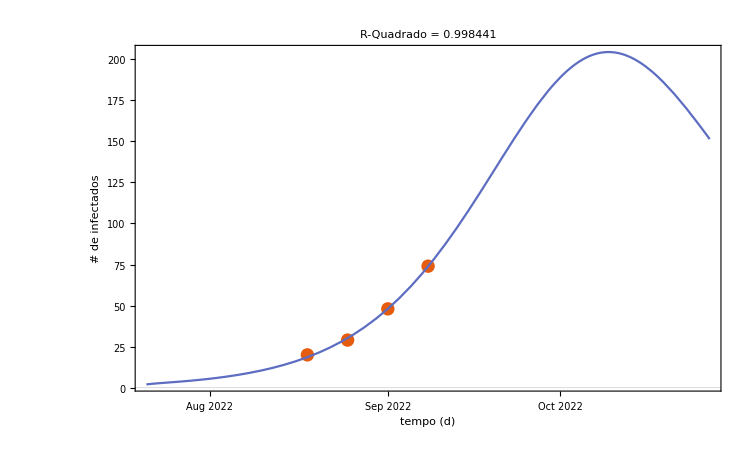

```mathematica
Quiet @ fitInfectedDynamic02["ParameterTable"]
Quiet @ fitInfectedDynamic02["BestFitParameters"]
Quiet @fitInfectedDynamic02["RSquared"]
Quiet @fitInfectedDynamic02["AdjustedRSquared"]
Quiet @FitWithDataPlot[fitInfectedDynamic02,{First@First@Normal[currentDynamic],First@Last@Normal[currentDynamic]} ]
```

### Simulação 3

```mathematica
AbsoluteTiming[fitInfectedDynamic03=NonlinearModelFit[s03,{infectedSolDynamic[t], {0<β && 0<α1<=1 && 0< α2<=1}},{{β,0.293}, {α1,0.355},{α2,0.0856}},t, AccuracyGoal-> 3, WorkingPrecision-> 3,  PrecisionGoal -> 3, EvaluationMonitor:> Print["β=", β,"  .α1=",α1,"   .α2=",α2],Method-> {NMinimize, Method->{"NelderMead", "PostProcess"-> {"FindMinimum"}}}]]
```

ParametricNDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

General::stop: Further output of ParametricNDSolve::ihist will be suppressed during this calculation.

β=0.293  .α1=0.355   .α2=0.0856

β=1.07973  .α1=0.833591   .α2=0.826558

β=0.627259  .α1=0.880957   .α2=0.420882

β=1.3341  .α1=0.327687   .α2=0.727544

β=0.42318  .α1=0.208838   .α2=0.042381

β=0.915591  .α1=0.677403   .α2=0.61895

β=0.587317  .α1=0.365026   .α2=0.203734

ParametricNDSolve::ndsz: At t == 26.6752, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {56.} lies outside the range of data in the interpolating function. Extrapolation will be used.

ParametricNDSolve::ndsz: At t == 26.6752, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {63.} lies outside the range of data in the interpolating function. Extrapolation will be used.

ParametricNDSolve::ndsz: At t == 26.6752, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolve::ndsz will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {70.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

β=0.00943698  .α1=0.739635   .α2=0.0302618

β=0.918315  .α1=0.430674   .α2=0.482142

β=0.571829  .α1=0.0796861   .α2=0.0934352

β=0.0497829  .α1=0.102468   .α2=0.00290346

β=0.701182  .α1=0.348622   .α2=0.304866

β=0.45669  .α1=0.157179   .α2=0.118866

β=0.391377  .α1=0.0532558   .α2=0.0764325

β=0.179831  .α1=0.0459546   .α2=0.0361089

β=0.570844  .α1=0.272955   .α2=0.202083

β=0.374845  .α1=0.25609   .α2=0.102233

β=0.45669  .α1=0.157179   .α2=0.118866

β=0.51426  .α1=0.118433   .α2=0.106151

β=0.578936  .α1=0.252901   .α2=0.211866

β=0.318261  .α1=0.101567   .α2=0.00630086

β=0.484629  .α1=0.0294763   .α2=0.0519788

β=0.402291  .α1=0.190908   .α2=0.0896696

β=0.597233  .α1=0.209446   .α2=0.20349

β=0.388004  .α1=0.128537   .α2=0.0555982

β=0.503678  .α1=0.0785246   .α2=0.0974073

β=0.427638  .α1=0.162812   .α2=0.091604

β=0.478331  .α1=0.10662   .α2=0.0954729

β=0.440311  .α1=0.148764   .α2=0.0925712

β=0.552837  .α1=0.154381   .α2=0.156127

β=0.429212  .α1=0.134998   .α2=0.0807305

β=0.49313  .α1=0.124976   .α2=0.111261

β=0.453516  .α1=0.142817   .α2=0.0972436

β=0.520432  .α1=0.143955   .α2=0.13411

β=0.439499  .α1=0.177535   .α2=0.127329

β=0.379372  .α1=0.174399   .α2=0.0948494

β=0.485167  .α1=0.151566   .α2=0.124295

β=0.414637  .α1=0.166788   .α2=0.104665

β=0.432269  .α1=0.162983   .α2=0.109572

β=0.432123  .α1=0.188981   .α2=0.139935

β=0.421426  .α1=0.212063   .α2=0.161281

β=0.453272  .α1=0.186147   .α2=0.147848

β=0.463774  .α1=0.19773   .α2=0.166986

β=0.455225  .α1=0.177337   .α2=0.14377

β=0.463088  .α1=0.177238   .α2=0.151991

β=0.437056  .α1=0.211131   .α2=0.168836

β=0.427239  .α1=0.238106   .α2=0.193821

β=0.464913  .α1=0.194096   .α2=0.167035

β=0.481307  .α1=0.196653   .α2=0.180585

β=0.451523  .α1=0.202228   .α2=0.171913

β=0.447103  .α1=0.227633   .α2=0.194752

β=0.443043  .α1=0.252781   .α2=0.220243

β=0.445151  .α1=0.236443   .α2=0.19883

β=0.465015  .α1=0.244416   .α2=0.221902

β=0.444046  .α1=0.219452   .α2=0.182102

β=0.423247  .α1=0.278355   .α2=0.233748

β=0.454496  .α1=0.215161   .α2=0.183713

β=0.433664  .α1=0.25729   .α2=0.21707

β=0.438872  .α1=0.246758   .α2=0.208731

β=0.438823  .α1=0.242884   .α2=0.208554

β=0.443569  .α1=0.238054   .α2=0.201261

β=0.43961  .α1=0.272276   .α2=0.238053

β=0.437392  .α1=0.298688   .α2=0.266029

β=0.445276  .α1=0.261983   .α2=0.230974

β=0.448478  .α1=0.269595   .α2=0.242095

β=0.441717  .α1=0.28664   .α2=0.258252

β=0.44218  .α1=0.274493   .α2=0.244005

β=0.441668  .α1=0.286387   .α2=0.255112

β=0.44098  .α1=0.30319   .α2=0.272547

β=0.441731  .α1=0.283806   .α2=0.250378

β=0.445715  .α1=0.29371   .α2=0.264546

β=0.441136  .α1=0.277635   .α2=0.244677

β=0.437288  .α1=0.314438   .α2=0.280761

β=0.437872  .α1=0.313035   .α2=0.281611

β=0.440766  .α1=0.291113   .α2=0.258186

β=0.43822  .α1=0.328193   .α2=0.296319

β=0.438949  .α1=0.315553   .α2=0.283409

β=0.443175  .α1=0.292133   .α2=0.262001

β=0.441703  .α1=0.297709   .α2=0.266691

β=0.44335  .α1=0.279122   .α2=0.248207

β=0.44005  .α1=0.306445   .α2=0.274608

β=0.441056  .α1=0.313783   .α2=0.284377

β=0.440839  .α1=0.296781   .α2=0.264734

β=0.440748  .α1=0.297434   .α2=0.264809

β=0.440922  .α1=0.301751   .α2=0.270612

β=0.439503  .α1=0.305609   .α2=0.273279

β=0.440053  .α1=0.303634   .α2=0.271632

β=0.44116  .α1=0.294998   .α2=0.263377

β=0.440882  .α1=0.29786   .α2=0.266185

β=0.4404  .α1=0.305382   .α2=0.274219

β=0.440729  .α1=0.298931   .α2=0.267105

β=0.440188  .α1=0.298533   .α2=0.266003

β=0.43982  .α1=0.296923   .α2=0.263698

β=0.441146  .α1=0.293249   .α2=0.26123

β=0.440326  .α1=0.301038   .α2=0.269031

β=0.439946  .α1=0.301141   .α2=0.268575

β=0.439479  .α1=0.302781   .α2=0.269769

β=0.439266  .α1=0.302636   .α2=0.26943

β=0.438535  .α1=0.304489   .α2=0.270593

β=0.438474  .α1=0.302831   .α2=0.268545

β=0.437548  .α1=0.303728   .α2=0.268302

β=0.436854  .α1=0.308799   .α2=0.273107

β=0.435187  .α1=0.313932   .α2=0.276659

β=0.435812  .α1=0.308563   .α2=0.271565

β=0.433979  .α1=0.311453   .α2=0.272463

β=0.433719  .α1=0.311498   .α2=0.271988

β=0.431311  .α1=0.315002   .α2=0.272686

β=0.430548  .α1=0.319775   .α2=0.277202

β=0.435798  .α1=0.307739   .α2=0.270527

β=0.430539  .α1=0.313997   .α2=0.270677

β=0.43112  .α1=0.313039   .α2=0.27013

β=0.42969  .α1=0.313832   .α2=0.268964

β=0.425229  .α1=0.320815   .α2=0.271024

β=0.433156  .α1=0.311008   .α2=0.270651

β=0.432232  .α1=0.312565   .α2=0.270857

β=0.429  .α1=0.316591   .α2=0.27102

β=0.426922  .α1=0.319382   .α2=0.271204

β=0.426383  .α1=0.31958   .α2=0.271046

β=0.424019  .α1=0.320194   .α2=0.268123

β=0.42737  .α1=0.316026   .α2=0.267815

β=0.42663  .α1=0.318691   .α2=0.270238

β=0.422024  .α1=0.325013   .α2=0.270746

β=0.427773  .α1=0.316627   .α2=0.26941

β=0.430198  .α1=0.316273   .α2=0.272445

β=0.425564  .α1=0.319214   .α2=0.269204

β=0.42497  .α1=0.321564   .α2=0.271021

β=0.425007  .α1=0.321416   .α2=0.270714

β=0.424196  .α1=0.322778   .α2=0.270953

β=0.425162  .α1=0.323269   .α2=0.272915

β=0.424961  .α1=0.325296   .α2=0.274771

β=0.425749  .α1=0.323407   .α2=0.273597

β=0.423015  .α1=0.328271   .α2=0.27501

β=0.421061  .α1=0.332716   .α2=0.276912

β=0.423652  .α1=0.331501   .α2=0.279234

β=0.420701  .α1=0.336269   .α2=0.280348

β=0.418648  .α1=0.341695   .α2=0.282892

β=0.415492  .α1=0.349894   .α2=0.286953

β=0.42154  .α1=0.334339   .α2=0.279012

β=0.417182  .α1=0.340998   .α2=0.279976

β=0.413947  .α1=0.345747   .α2=0.280347

β=0.416387  .α1=0.342601   .α2=0.280842

β=0.420252  .α1=0.336404   .α2=0.279469

β=0.416326  .α1=0.346682   .α2=0.284646

β=0.417192  .α1=0.341029   .α2=0.279836

β=0.416464  .α1=0.340696   .α2=0.278308

β=0.420091  .α1=0.332272   .α2=0.274875

β=0.417268  .α1=0.34308   .α2=0.282203

β=0.414175  .α1=0.347   .α2=0.281874

β=0.418733  .α1=0.339053   .α2=0.280071

β=0.41828  .α1=0.341109   .α2=0.28143

β=0.418829  .α1=0.341165   .α2=0.282157

β=0.416427  .α1=0.344425   .α2=0.282242

β=0.415274  .α1=0.347111   .α2=0.283328

β=0.416563  .α1=0.343086   .α2=0.280859

β=0.416219  .α1=0.346509   .α2=0.283909

β=0.415732  .α1=0.34925   .α2=0.285946

β=0.413432  .α1=0.351855   .α2=0.285325

β=0.413063  .α1=0.355725   .α2=0.288873

β=0.415688  .α1=0.346246   .α2=0.282863

β=0.414628  .α1=0.351123   .α2=0.286095

β=0.414305  .α1=0.353129   .α2=0.287478

β=0.413292  .α1=0.356577   .α2=0.289636

β=0.412095  .α1=0.361742   .α2=0.293023

β=0.415454  .α1=0.354115   .α2=0.290048

β=0.413938  .α1=0.35242   .α2=0.286506

β=0.411958  .α1=0.358834   .α2=0.289801

β=0.410071  .α1=0.363626   .α2=0.291729

β=0.411175  .α1=0.363134   .α2=0.292723

β=0.409793  .α1=0.368491   .α2=0.295831

β=0.407799  .α1=0.372667   .α2=0.29732

β=0.412679  .α1=0.358013   .α2=0.289938

β=0.408403  .α1=0.370177   .α2=0.295362

β=0.405958  .α1=0.376977   .α2=0.298225

β=0.404536  .α1=0.381383   .α2=0.300585

β=0.410643  .α1=0.363856   .α2=0.2926

β=0.407525  .α1=0.375923   .α2=0.299375

β=0.406252  .α1=0.382072   .α2=0.303199

β=0.404026  .α1=0.387837   .α2=0.30557

β=0.408989  .α1=0.369851   .α2=0.295843

β=0.40434  .α1=0.384109   .α2=0.302347

β=0.401613  .α1=0.391918   .α2=0.305604

β=0.402045  .α1=0.392254   .α2=0.306671

β=0.407253  .α1=0.375452   .α2=0.29855

β=0.405939  .α1=0.384111   .α2=0.304505

β=0.405953  .α1=0.378761   .α2=0.299795

β=0.405445  .α1=0.376809   .α2=0.297262

β=0.406051  .α1=0.380756   .α2=0.301715

β=0.40434  .α1=0.384109   .α2=0.302347

β=0.40434  .α1=0.384109   .α2=0.302347

β=0.40434  .α1=0.384109   .α2=0.302347

«8 more identical outputs»

β=0.773583  .α1=0.622413   .α2=0.0638707

β=0.773583  .α1=0.622413   .α2=0.0638707

β=0.773583  .α1=0.622413   .α2=0.0638707

«2 more identical outputs»

β=0.406744  .α1=0.385661   .α2=0.300794

β=0.406744  .α1=0.385661   .α2=0.300794

β=0.406744  .α1=0.385661   .α2=0.300794

«2 more identical outputs»

β=0.404447  .α1=0.384178   .α2=0.302277

β=0.404447  .α1=0.384178   .α2=0.302277

β=0.404447  .α1=0.384178   .α2=0.302277

«2 more identical outputs»

β=0.404449  .α1=0.384185   .α2=0.302277

β=0.404449  .α1=0.384185   .α2=0.302277

β=0.404449  .α1=0.384185   .α2=0.302277

«2 more identical outputs»

β=0.404445  .α1=0.384187   .α2=0.302274

β=0.404445  .α1=0.384187   .α2=0.302274

β=0.404445  .α1=0.384187   .α2=0.302274

«2 more identical outputs»

β=0.40443  .α1=0.384199   .α2=0.302265

β=0.40443  .α1=0.384199   .α2=0.302265

β=0.40443  .α1=0.384199   .α2=0.302265

«2 more identical outputs»

β=0.404368  .α1=0.384244   .α2=0.302227

β=0.404368  .α1=0.384244   .α2=0.302227

β=0.404368  .α1=0.384244   .α2=0.302227

«2 more identical outputs»

β=0.402222  .α1=0.385926   .α2=0.300803

β=0.402222  .α1=0.385926   .α2=0.300803

β=0.402222  .α1=0.385926   .α2=0.300803

«2 more identical outputs»

β=0.403826  .α1=0.384669   .α2=0.301868

β=0.403826  .α1=0.384669   .α2=0.301868

β=0.403826  .α1=0.384669   .α2=0.301868

«2 more identical outputs»

β=0.403209  .α1=0.385176   .α2=0.30143

β=0.403209  .α1=0.385176   .α2=0.30143

β=0.403209  .α1=0.385176   .α2=0.30143

«2 more identical outputs»

β=0.402964  .α1=0.385409   .α2=0.301224

β=0.402964  .α1=0.385409   .α2=0.301224

β=0.402964  .α1=0.385409   .α2=0.301224

«2 more identical outputs»

β=0.401599  .α1=0.386805   .α2=0.299957

β=0.401599  .α1=0.386805   .α2=0.299957

β=0.401599  .α1=0.386805   .α2=0.299957

«2 more identical outputs»

β=0.397283  .α1=0.390864   .α2=0.296357

β=0.397283  .α1=0.390864   .α2=0.296357

β=0.397283  .α1=0.390864   .α2=0.296357

«2 more identical outputs»

β=0.372815  .α1=0.413606   .α2=0.276253

β=0.372815  .α1=0.413606   .α2=0.276253

β=0.372815  .α1=0.413606   .α2=0.276253

«2 more identical outputs»

β=0.392159  .α1=0.395626   .α2=0.292147

β=0.392159  .α1=0.395626   .α2=0.292147

β=0.392159  .α1=0.395626   .α2=0.292147

«2 more identical outputs»

β=0.38796  .α1=0.399545   .α2=0.288673

β=0.38796  .α1=0.399545   .α2=0.288673

β=0.38796  .α1=0.399545   .α2=0.288673

«2 more identical outputs»

β=0.391503  .α1=0.396239   .α2=0.291604

β=0.391503  .α1=0.396239   .α2=0.291604

β=0.391503  .α1=0.396239   .α2=0.291604

«2 more identical outputs»

β=0.392054  .α1=0.395724   .α2=0.29206

β=0.392054  .α1=0.395724   .α2=0.29206

β=0.392054  .α1=0.395724   .α2=0.29206

«2 more identical outputs»

β=0.392139  .α1=0.395645   .α2=0.292131

β=0.392139  .α1=0.395645   .α2=0.292131

β=0.392139  .α1=0.395645   .α2=0.292131

«2 more identical outputs»

β=0.392153  .α1=0.395632   .α2=0.292142

β=0.392153  .α1=0.395632   .α2=0.292142

β=0.392153  .α1=0.395632   .α2=0.292142

«2 more identical outputs»

β=0.392158  .α1=0.395627   .α2=0.292146

β=0.392158  .α1=0.395627   .α2=0.292146

β=0.392158  .α1=0.395627   .α2=0.292146

«2 more identical outputs»

β=0.392159  .α1=0.395627   .α2=0.292147

β=0.392159  .α1=0.395627   .α2=0.292147

β=0.392159  .α1=0.395627   .α2=0.292147

«2 more identical outputs»

β=0.392159  .α1=0.395626   .α2=0.292147

β=0.392159  .α1=0.395626   .α2=0.292147

β=0.392159  .α1=0.395626   .α2=0.292147

«12 more identical outputs»

β=0.392147  .α1=0.395625   .α2=0.292152

β=0.392147  .α1=0.395625   .α2=0.292152

β=0.392147  .α1=0.395625   .α2=0.292152

«2 more identical outputs»

β=0.392134  .α1=0.395636   .α2=0.292156

β=0.392134  .α1=0.395636   .α2=0.292156

β=0.392134  .α1=0.395636   .α2=0.292156

«2 more identical outputs»

β=0.392128  .α1=0.395638   .α2=0.292158

β=0.392128  .α1=0.395638   .α2=0.292158

β=0.392128  .α1=0.395638   .α2=0.292158

«2 more identical outputs»

β=0.392105  .α1=0.395647   .α2=0.292166

β=0.392105  .α1=0.395647   .α2=0.292166

β=0.392105  .α1=0.395647   .α2=0.292166

«2 more identical outputs»

β=0.392124  .α1=0.39564   .α2=0.292159

β=0.392124  .α1=0.39564   .α2=0.292159

β=0.392124  .α1=0.39564   .α2=0.292159

«2 more identical outputs»

β=0.392128  .α1=0.395637   .α2=0.292158

β=0.392128  .α1=0.395637   .α2=0.292158

β=0.392128  .α1=0.395637   .α2=0.292158

«2 more identical outputs»

β=14.009  .α1=-7.30112   .α2=-4.25818

β=14.009  .α1=-7.30112   .α2=-4.25818

β=14.009  .α1=-7.30112   .α2=-4.25818

«2 more identical outputs»

β=4.9311  .α1=-2.16995   .α2=-1.22462

β=4.9311  .α1=-2.16995   .α2=-1.22462

β=4.9311  .α1=-2.16995   .α2=-1.22462

«2 more identical outputs»

β=0.392128  .α1=0.395637   .α2=0.292158

β=0.40434  .α1=0.384109   .α2=0.302347

β=0.392128  .α1=0.395637   .α2=0.292158

β=0.392128  .α1=0.395637   .α2=0.292158

β=0.392128  .α1=0.395637   .α2=0.292158

«2 more identical outputs»

β=0.747668  .α1=0.626971   .α2=0.556877

β=0.747668  .α1=0.626971   .α2=0.556877

β=0.747668  .α1=0.626971   .α2=0.556877

«2 more identical outputs»

β=0.392399  .α1=0.395813   .α2=0.292359

β=0.392399  .α1=0.395813   .α2=0.292359

β=0.392399  .α1=0.395813   .α2=0.292359

«2 more identical outputs»

β=0.392147  .α1=0.39565   .α2=0.292172

β=0.392147  .α1=0.39565   .α2=0.292172

β=0.392147  .α1=0.39565   .α2=0.292172

«2 more identical outputs»

β=0.392206  .α1=0.395702   .α2=0.292293

β=0.392206  .α1=0.395702   .α2=0.292293

β=0.392206  .α1=0.395702   .α2=0.292293

«2 more identical outputs»

β=0.392288  .α1=0.395772   .α2=0.292516

β=0.392288  .α1=0.395772   .α2=0.292516

β=0.392288  .α1=0.395772   .α2=0.292516

«2 more identical outputs»

β=5.77902  .α1=5.00031   .α2=14.9618

β=5.77902  .α1=5.00031   .α2=14.9618

β=5.77902  .α1=5.00031   .α2=14.9618

«2 more identical outputs»

β=0.41774  .α1=0.417528   .α2=0.361829

β=0.41774  .α1=0.417528   .α2=0.361829

β=0.41774  .α1=0.417528   .α2=0.361829

«2 more identical outputs»

β=0.393398  .α1=0.39672   .α2=0.295539

β=0.393398  .α1=0.39672   .α2=0.295539

β=0.393398  .α1=0.39672   .α2=0.295539

«2 more identical outputs»

β=0.418166  .α1=0.417991   .α2=0.361847

β=0.418166  .α1=0.417991   .α2=0.361847

β=0.418166  .α1=0.417991   .α2=0.361847

«2 more identical outputs»

β=0.395099  .α1=0.398181   .α2=0.300093

β=0.395099  .α1=0.398181   .α2=0.300093

β=0.395099  .α1=0.398181   .α2=0.300093

«2 more identical outputs»

β=0.393762  .α1=0.397033   .α2=0.296513

β=0.393762  .α1=0.397033   .α2=0.296513

β=0.393762  .α1=0.397033   .α2=0.296513

«2 more identical outputs»

β=0.393541  .α1=0.396844   .α2=0.295923

β=0.393541  .α1=0.396844   .α2=0.295923

β=0.393541  .α1=0.396844   .α2=0.295923

«2 more identical outputs»

β=0.393433  .α1=0.396751   .α2=0.295634

β=0.393433  .α1=0.396751   .α2=0.295634

β=0.393433  .α1=0.396751   .α2=0.295634

«2 more identical outputs»

β=0.393408  .α1=0.396729   .α2=0.295565

β=0.393408  .α1=0.396729   .α2=0.295565

β=0.393408  .α1=0.396729   .α2=0.295565

«2 more identical outputs»

β=0.393401  .α1=0.396723   .α2=0.295547

β=0.393401  .α1=0.396723   .α2=0.295547

β=0.393401  .α1=0.396723   .α2=0.295547

«2 more identical outputs»

β=0.393398  .α1=0.396721   .α2=0.295541

β=0.393398  .α1=0.396721   .α2=0.295541

β=0.393398  .α1=0.396721   .α2=0.295541

«1 more identical outputs»

β=0.393399  .α1=0.396721   .α2=0.295541

β=0.393398  .α1=0.396721   .α2=0.295539

β=0.393398  .α1=0.396721   .α2=0.295539

β=0.393398  .α1=0.396721   .α2=0.295539

«2 more identical outputs»

β=0.393398  .α1=0.39672   .α2=0.295539

β=0.393398  .α1=0.39672   .α2=0.295539

β=0.393398  .α1=0.39672   .α2=0.295539

«7 more identical outputs»

β=0.393406  .α1=0.396728   .α2=0.295516

β=0.393406  .α1=0.396728   .α2=0.295516

β=0.393406  .α1=0.396728   .α2=0.295516

«2 more identical outputs»

β=0.393448  .α1=0.396751   .α2=0.295428

β=0.393448  .α1=0.396751   .α2=0.295428

β=0.393448  .α1=0.396751   .α2=0.295428

«2 more identical outputs»

β=0.393439  .α1=0.396765   .α2=0.295419

β=0.393439  .α1=0.396765   .α2=0.295419

β=0.393439  .α1=0.396765   .α2=0.295419

«2 more identical outputs»

β=0.393444  .α1=0.396757   .α2=0.295424

β=0.393444  .α1=0.396757   .α2=0.295424

β=0.393444  .α1=0.396757   .α2=0.295424

«2 more identical outputs»

β=0.393439  .α1=0.396761   .α2=0.295425

β=0.393439  .α1=0.396761   .α2=0.295425

β=0.393439  .α1=0.396761   .α2=0.295425

«2 more identical outputs»

β=0.393441  .α1=0.396758   .α2=0.295427

β=0.393441  .α1=0.396758   .α2=0.295427

β=0.393441  .α1=0.396758   .α2=0.295427

«2 more identical outputs»

β=0.39344  .α1=0.39676   .α2=0.295426

β=0.39344  .α1=0.39676   .α2=0.295426

β=0.39344  .α1=0.39676   .α2=0.295426

«2 more identical outputs»

β=0.39344  .α1=0.39676   .α2=0.295425

β=0.39344  .α1=0.39676   .α2=0.295425

β=0.39344  .α1=0.39676   .α2=0.295425

«2 more identical outputs»

β=0.393439  .α1=0.396761   .α2=0.295425

β=0.393439  .α1=0.396761   .α2=0.295425

β=0.393439  .α1=0.396761   .α2=0.295425

«12 more identical outputs»

β=0.39344  .α1=0.396761   .α2=0.295425

β=0.39344  .α1=0.396761   .α2=0.295425

β=0.39344  .α1=0.396761   .α2=0.295425

«2 more identical outputs»

β=0.393439  .α1=0.396761   .α2=0.295425

β=0.393439  .α1=0.396761   .α2=0.295425

β=0.393439  .α1=0.396761   .α2=0.295425

«12 more identical outputs»

β=0.393439  .α1=0.396762   .α2=0.295425

β=0.393439  .α1=0.396762   .α2=0.295425

β=0.393439  .α1=0.396762   .α2=0.295425

«2 more identical outputs»

β=0.393439  .α1=0.396761   .α2=0.295425

β=0.393439  .α1=0.396761   .α2=0.295425

β=0.393439  .α1=0.396761   .α2=0.295425

«2 more identical outputs»

β=0.393439  .α1=0.396762   .α2=0.295425

β=0.393439  .α1=0.396762   .α2=0.295425

β=0.393439  .α1=0.396762   .α2=0.295425

«53 more identical outputs»

β=0.392128  .α1=0.395637   .α2=0.292158

β=0.393439  .α1=0.396762   .α2=0.295425

β=0.393439  .α1=0.396762   .α2=0.295425

β=0.393439  .α1=0.396762   .α2=0.295425

«2 more identical outputs»

β=0.267666  .α1=0.0461587   .α2=-0.0381296

β=0.267666  .α1=0.0461587   .α2=-0.0381296

β=0.267666  .α1=0.0461588   .α2=-0.0381296

β=0.267666  .α1=0.0461587   .α2=-0.0381296

β=0.267666  .α1=0.0461587   .α2=-0.0381296

β=0.393411  .α1=0.396684   .α2=0.295351

β=0.393411  .α1=0.396684   .α2=0.295351

β=0.393411  .α1=0.396684   .α2=0.295351

«2 more identical outputs»

β=0.393434  .α1=0.396749   .α2=0.295413

β=0.393434  .α1=0.396749   .α2=0.295413

β=0.393434  .α1=0.396749   .α2=0.295413

«2 more identical outputs»

β=0.393438  .α1=0.39676   .α2=0.295424

β=0.393438  .α1=0.39676   .α2=0.295424

β=0.393438  .α1=0.39676   .α2=0.295424

«2 more identical outputs»

β=0.393439  .α1=0.396761   .α2=0.295425

β=0.393439  .α1=0.396761   .α2=0.295425

β=0.393439  .α1=0.396761   .α2=0.295425

«2 more identical outputs»

β=0.393439  .α1=0.396762   .α2=0.295425

β=0.393439  .α1=0.396762   .α2=0.295425

β=0.393439  .α1=0.396762   .α2=0.295425

«35 more identical outputs»

ParametricNDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

{949.062,FittedModel[InterpolatingFunction[…][t]]}

| Estimate | Standard Error | t-Statistic | P-Value
β | 0.393 | 0.909174 | 0.432743 | 0.739998
α1 | 0.397 | 2.55055 | 0.155559 | 0.901755
α2 | 0.295 | 0.756811 | 0.390356 | 0.763073

{β→0.393,α1→0.397,α2→0.295}

0.998821

0.995284

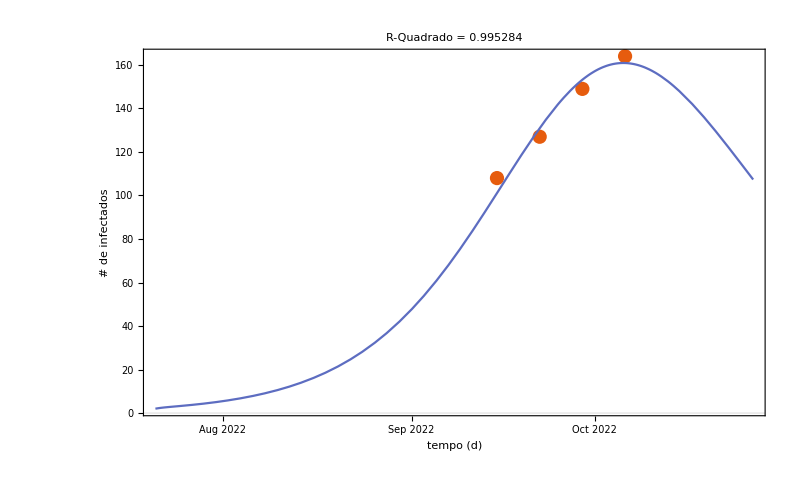

```mathematica
Quiet @ fitInfectedDynamic03["ParameterTable"]
Quiet @ fitInfectedDynamic03["BestFitParameters"]
Quiet @fitInfectedDynamic03["RSquared"]
Quiet @fitInfectedDynamic03["AdjustedRSquared"]
Quiet @FitWithDataPlot[fitInfectedDynamic03,{First@First@Normal[currentDynamic],First@Last@Normal[currentDynamic]} ]
```

### Simulação 4

```mathematica
AbsoluteTiming[fitInfectedDynamic04=NonlinearModelFit[s04,{infectedSolDynamic[t], {0<β && 0<α1<=1 && 0< α2<=1}},{{β,0.393}, {α1,0.397},{α2,0.295}},t, AccuracyGoal-> 3, WorkingPrecision-> 3,  PrecisionGoal -> 3, EvaluationMonitor:> Print["β=", β,"  .α1=",α1,"   .α2=",α2],Method-> {NMinimize, Method->{"NelderMead", "PostProcess"-> {"FindMinimum"}}}]]
```

ParametricNDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

General::stop: Further output of ParametricNDSolve::ihist will be suppressed during this calculation.

β=0.393  .α1=0.397   .α2=0.295

β=1.07973  .α1=0.833591   .α2=0.826558

β=0.627259  .α1=0.880957   .α2=0.420882

β=1.3341  .α1=0.327687   .α2=0.727544

β=0.489847  .α1=0.236838   .α2=0.135726

ParametricNDSolve::ndsz: At t == 33.2508, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {84.} lies outside the range of data in the interpolating function. Extrapolation will be used.

ParametricNDSolve::ndsz: At t == 33.2508, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {91.} lies outside the range of data in the interpolating function. Extrapolation will be used.

ParametricNDSolve::ndsz: At t == 33.2508, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolve::ndsz will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {98.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

β=0.850709  .α1=0.042381   .α2=0.351298

β=0.683121  .α1=0.600733   .α2=0.403486

β=0.00943698  .α1=0.49536   .α2=0.0302618

β=0.928047  .α1=0.369605   .α2=0.502808

β=0.524141  .α1=0.0682296   .α2=0.21887

β=0.643376  .α1=0.467607   .α2=0.357332

β=0.0894352  .α1=0.364691   .α2=0.0225646

β=0.718394  .α1=0.368377   .α2=0.382747

β=0.424118  .α1=0.200536   .α2=0.184983

β=0.152916  .α1=0.187873   .α2=0.0277262

β=0.577024  .α1=0.323251   .α2=0.293992

β=0.294285  .α1=0.232999   .α2=0.116481

β=0.36497  .α1=0.255562   .α2=0.160859

β=0.298212  .α1=0.331894   .α2=0.291502

β=0.441938  .α1=0.260602   .α2=0.17467

β=0.34612  .α1=0.30813   .α2=0.252558

β=0.417984  .α1=0.272484   .α2=0.194142

β=0.359851  .α1=0.416161   .α2=0.248351

β=0.36887  .α1=0.232471   .α2=0.107235

β=0.356805  .α1=0.150207   .α2=0.0133518

β=0.311144  .α1=0.330312   .α2=0.150154

β=0.336805  .α1=0.129402   .α2=0.0304809

β=0.325281  .α1=0.00796861   .α2=0.000290346

β=0.402619  .α1=0.0813117   .α2=0.0488956

β=0.334013  .α1=0.268062   .α2=0.124839

β=0.328155  .α1=0.164395   .α2=0.0141776

β=0.355766  .α1=0.23277   .α2=0.124189

β=0.315519  .α1=0.187685   .α2=0.0791048

β=0.355532  .α1=0.221275   .α2=0.100202

β=0.328857  .α1=0.198882   .α2=0.0861372

β=0.348864  .α1=0.215676   .α2=0.0966859

β=0.324021  .α1=0.17599   .α2=0.0438155

β=0.34783  .α1=0.218575   .α2=0.104095

β=0.350333  .α1=0.338807   .α2=0.186599

β=0.340187  .α1=0.181753   .α2=0.0695106

β=0.357241  .α1=0.142608   .α2=0.0553551

β=0.368855  .α1=0.0798813   .α2=0.020613

β=0.347975  .α1=0.146281   .α2=0.0559548

β=0.349105  .α1=0.0951868   .α2=0.0164517

β=0.348786  .α1=0.126034   .α2=0.0383626

β=0.362481  .α1=0.0948623   .α2=0.0302711

β=0.34576  .α1=0.160031   .α2=0.0597007

β=0.351864  .α1=0.173246   .α2=0.0756445

β=0.351095  .α1=0.161443   .α2=0.066324

β=0.358447  .α1=0.140191   .α2=0.058722

β=0.348932  .α1=0.155071   .α2=0.059456

β=0.35687  .α1=0.1598   .α2=0.064802

β=0.350199  .α1=0.149661   .α2=0.0581666

β=0.34291  .α1=0.168175   .α2=0.067276

β=0.353658  .α1=0.149   .α2=0.0583353

β=0.350764  .α1=0.141045   .α2=0.0509813

β=0.354149  .α1=0.138066   .α2=0.0521995

β=0.356757  .α1=0.129564   .α2=0.0485712

β=0.34975  .α1=0.136848   .α2=0.0492296

β=0.352681  .α1=0.145962   .α2=0.0560589

β=0.353921  .α1=0.148082   .α2=0.0599687

β=0.351553  .α1=0.142804   .α2=0.0532281

β=0.35539  .α1=0.134894   .α2=0.0494911

β=0.351496  .α1=0.145969   .α2=0.0559977

β=0.352118  .α1=0.138598   .α2=0.051558

β=0.35254  .α1=0.144121   .α2=0.0549337

β=0.349578  .α1=0.15053   .α2=0.0572402

β=0.353006  .α1=0.141182   .α2=0.0534597

β=0.353142  .α1=0.144711   .α2=0.0563659

β=0.352745  .α1=0.144234   .α2=0.0555815

β=0.352291  .α1=0.14347   .α2=0.0550922

β=0.352478  .α1=0.143958   .α2=0.0549733

β=0.351909  .α1=0.143172   .α2=0.054039

β=0.353432  .α1=0.139572   .α2=0.0523169

β=0.35198  .α1=0.14437   .α2=0.0550775

β=0.351239  .α1=0.146485   .α2=0.0559336

β=0.352564  .α1=0.142508   .α2=0.0540781

β=0.352773  .α1=0.144052   .α2=0.0553803

β=0.352125  .α1=0.143392   .α2=0.0543743

β=0.351968  .α1=0.142888   .α2=0.0540467

β=0.352458  .α1=0.141489   .α2=0.0532552

β=0.3521  .α1=0.14365   .α2=0.054622

β=0.352557  .α1=0.143478   .α2=0.0546696

β=0.352116  .α1=0.143036   .α2=0.0542024

β=0.352395  .α1=0.142737   .α2=0.0542273

β=0.352192  .α1=0.143228   .α2=0.0543376

β=0.351708  .α1=0.144101   .α2=0.0546965

β=0.351279  .α1=0.144898   .α2=0.0550057

β=0.351884  .α1=0.144284   .α2=0.0549016

β=0.352058  .α1=0.143348   .α2=0.0543772

β=0.351718  .α1=0.144171   .α2=0.0547929

β=0.352074  .α1=0.143464   .α2=0.0544514

β=0.351793  .α1=0.143626   .α2=0.0543948

β=0.35164  .α1=0.143614   .α2=0.0542812

β=0.352242  .α1=0.142857   .α2=0.0541191

β=0.351841  .α1=0.14379   .α2=0.0545521

β=0.351793  .α1=0.143626   .α2=0.0543948

β=0.351793  .α1=0.143626   .α2=0.0543948

β=0.351793  .α1=0.143626   .α2=0.0543948

«8 more identical outputs»

β=0.11956  .α1=-0.109575   .α2=0.417654

β=0.11956  .α1=-0.109575   .α2=0.417654

β=0.11956  .α1=-0.109575   .α2=0.417654

«2 more identical outputs»

β=0.274382  .α1=0.0592257   .α2=0.175481

β=0.274382  .α1=0.0592257   .α2=0.175481

β=0.274382  .α1=0.0592257   .α2=0.175481

«2 more identical outputs»

β=0.325989  .α1=0.115492   .α2=0.0947569

β=0.325989  .α1=0.115492   .α2=0.0947569

β=0.325989  .α1=0.115492   .α2=0.0947569

«2 more identical outputs»

β=0.351788  .α1=0.14362   .α2=0.0544028

β=0.351788  .α1=0.14362   .α2=0.0544028

β=0.351788  .α1=0.14362   .α2=0.0544028

«2 more identical outputs»

β=0.351787  .α1=0.14362   .α2=0.0544074

β=0.351787  .α1=0.14362   .α2=0.0544074

β=0.351787  .α1=0.14362   .α2=0.0544074

«2 more identical outputs»

β=0.351787  .α1=0.14362   .α2=0.0544075

β=0.351787  .α1=0.14362   .α2=0.0544075

β=0.351787  .α1=0.14362   .α2=0.0544075

«2 more identical outputs»

β=0.351787  .α1=0.14362   .α2=0.0544074

β=0.351787  .α1=0.14362   .α2=0.0544074

β=0.351787  .α1=0.14362   .α2=0.0544074

«12 more identical outputs»

β=0.351784  .α1=0.143617   .α2=0.054411

β=0.351784  .α1=0.143617   .α2=0.054411

β=0.351784  .α1=0.143617   .α2=0.054411

«2 more identical outputs»

β=0.351787  .α1=0.14362   .α2=0.0544075

β=0.351787  .α1=0.14362   .α2=0.0544075

β=0.351787  .α1=0.14362   .α2=0.0544075

«2 more identical outputs»

β=0.351787  .α1=0.14362   .α2=0.0544074

β=0.351787  .α1=0.14362   .α2=0.0544074

β=0.351787  .α1=0.14362   .α2=0.0544074

«2 more identical outputs»

β=0.351786  .α1=0.14362   .α2=0.0544078

β=0.351786  .α1=0.14362   .α2=0.0544078

β=0.351786  .α1=0.14362   .α2=0.0544078

«2 more identical outputs»

β=0.351786  .α1=0.14362   .α2=0.0544076

β=0.351786  .α1=0.14362   .α2=0.0544076

β=0.351786  .α1=0.14362   .α2=0.0544076

«2 more identical outputs»

β=0.351787  .α1=0.14362   .α2=0.0544074

β=0.351787  .α1=0.14362   .α2=0.0544074

β=0.351787  .α1=0.14362   .α2=0.0544074

β=0.351787  .α1=0.14362   .α2=0.0544075

β=0.351787  .α1=0.14362   .α2=0.0544074

β=0.351787  .α1=0.14362   .α2=0.0544074

β=0.351787  .α1=0.14362   .α2=0.0544074

«8 more identical outputs»

β=-12.9322  .α1=3.42745   .α2=-2.00839

β=-12.9322  .α1=3.42745   .α2=-2.00839

β=-12.9322  .α1=3.42745   .α2=-2.00839

«2 more identical outputs»

β=0.351787  .α1=0.14362   .α2=0.0544074

β=0.351793  .α1=0.143626   .α2=0.0543948

β=0.351787  .α1=0.14362   .α2=0.0544074

ParametricNDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

{232.61,FittedModel[InterpolatingFunction[…][t]]}

Missing[]

{β→0.352,α1→0.144,α2→0.0544}

0.99865

ComplexInfinity

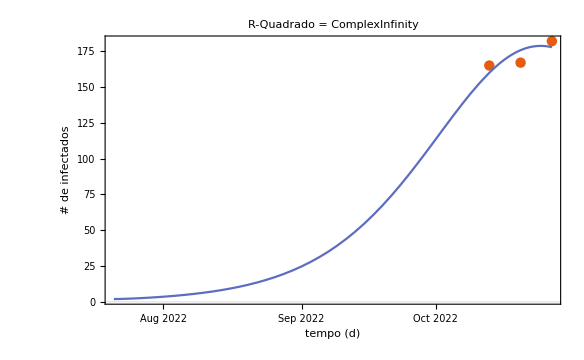

```mathematica
Quiet @ fitInfectedDynamic04["ParameterTable"]
Quiet @ fitInfectedDynamic04["BestFitParameters"]
Quiet @fitInfectedDynamic04["RSquared"]
Quiet @fitInfectedDynamic04["AdjustedRSquared"]
Quiet @FitWithDataPlot[fitInfectedDynamic04,{First@First@Normal[currentDynamic],First@Last@Normal[currentDynamic]} ]
```

```mathematica
AbsoluteTiming[fitInfectedDynamicAll=NonlinearModelFit[all,{infectedSolDynamic[t], {0<β && 0<α1<=1 && 0< α2<=1}},{{β,0.517}, {α1,0.729},{α2,0.692}},t, AccuracyGoal-> 3, WorkingPrecision-> 3,  PrecisionGoal -> 3, EvaluationMonitor:> Print["β=", β,"  .α1=",α1,"   .α2=",α2],Method-> {NMinimize, Method->{"NelderMead", "PostProcess"-> {"FindMinimum"}}}]]
```

ParametricNDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

General::stop: Further output of ParametricNDSolve::ihist will be suppressed during this calculation.

β=0.517  .α1=0.729   .α2=0.692

β=1.07973  .α1=0.833591   .α2=0.826558

β=0.627259  .α1=0.880957   .α2=0.420882

β=1.3341  .α1=0.327687   .α2=0.727544

β=1.32663  .α1=0.379228   .α2=0.957619

β=1.03876  .α1=0.123686   .α2=0.758218

β=0.58749  .α1=0.493589   .α2=0.87768

ParametricNDSolve::ndsz: At t == 35.6561, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolve::ndsz will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {42.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {49.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {56.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

β=0.214182  .α1=0.576541   .α2=0.952748

β=0.102204  .α1=0.518288   .α2=0.594313

β=1.02052  .α1=0.413993   .α2=0.866792

β=0.40831  .α1=0.483523   .α2=0.685139

β=0.00943698  .α1=0.969738   .α2=0.744995

β=0.771514  .α1=0.346195   .α2=0.754912

β=0.661209  .α1=0.153205   .α2=0.853154

β=0.553052  .α1=0.585051   .α2=0.732289

β=0.866394  .α1=0.466367   .α2=0.891448

β=0.522831  .α1=0.479234   .α2=0.736716

β=0.701504  .α1=0.294294   .α2=0.84725

β=0.590165  .α1=0.512362   .α2=0.761029

β=0.362143  .α1=0.643929   .α2=0.828705

β=0.669171  .α1=0.420628   .α2=0.77336

β=0.596163  .α1=0.416606   .α2=0.830809

β=0.591665  .α1=0.488423   .α2=0.778474

β=0.465486  .α1=0.553536   .α2=0.821887

β=0.61825  .α1=0.453855   .α2=0.785492

β=0.567674  .α1=0.454086   .α2=0.656108

β=0.557766  .α1=0.434334   .α2=0.545322

β=0.662228  .α1=0.451675   .α2=0.743333

β=0.55768  .α1=0.472344   .α2=0.73837

β=0.52643  .α1=0.48938   .α2=0.663143

β=0.480519  .α1=0.507143   .α2=0.601969

β=0.478918  .α1=0.467292   .α2=0.552491

β=0.422545  .α1=0.456727   .α2=0.4395

β=0.406155  .α1=0.50339   .α2=0.530451

β=0.527294  .α1=0.466412   .α2=0.624694

β=0.395892  .α1=0.481176   .α2=0.372405

β=0.314998  .α1=0.485592   .α2=0.189422

β=0.284747  .α1=0.499896   .α2=0.1959

β=0.201007  .α1=0.454334   .α2=0.00796861

β=0.410641  .α1=0.493941   .α2=0.438455

β=0.480709  .α1=0.45761   .α2=0.515684

β=0.333737  .α1=0.489325   .α2=0.275846

β=0.283706  .α1=0.522512   .α2=0.162982

β=0.214287  .α1=0.555404   .α2=0.0247224

β=0.210986  .α1=0.504345   .α2=0.0000290346

β=0.206056  .α1=0.518975   .α2=0.000361089

β=0.301817  .α1=0.496737   .α2=0.196662

β=0.389361  .α1=0.498882   .α2=0.366014

β=0.25558  .α1=0.502979   .α2=0.0915253

β=0.245738  .α1=0.529226   .α2=0.111357

β=0.297683  .α1=0.496501   .α2=0.169905

β=0.256162  .α1=0.517924   .α2=0.08628

β=0.233335  .α1=0.528518   .α2=0.0310892

β=0.232616  .α1=0.532443   .α2=0.0572857

β=0.281416  .α1=0.505486   .α2=0.141751

β=0.245066  .α1=0.495082   .α2=0.0500557

β=0.254726  .α1=0.501939   .α2=0.0782871

β=0.272623  .α1=0.51392   .α2=0.112686

β=0.259841  .α1=0.505715   .α2=0.0968156

β=0.232403  .α1=0.511566   .α2=0.0325046

β=0.207897  .α1=0.514605   .α2=0.0000294763

β=0.235687  .α1=0.515238   .α2=0.0345656

β=0.253802  .α1=0.508095   .α2=0.0812531

β=0.240186  .α1=0.523118   .α2=0.0550713

β=0.228099  .α1=0.510595   .α2=0.0262727

β=0.249146  .α1=0.516092   .α2=0.0712782

β=0.26302  .α1=0.519971   .α2=0.105897

β=0.240057  .α1=0.513667   .α2=0.0508527

β=0.255152  .α1=0.502119   .α2=0.080518

β=0.243927  .α1=0.517868   .α2=0.061433

β=0.234952  .α1=0.523656   .α2=0.0411228

β=0.24909  .α1=0.511986   .α2=0.0712205

β=0.254718  .α1=0.516963   .α2=0.0851017

β=0.243723  .α1=0.514491   .α2=0.059415

β=0.242013  .α1=0.513471   .α2=0.0567675

β=0.247363  .α1=0.515437   .α2=0.0676505

β=0.240919  .α1=0.519878   .α2=0.0544451

β=0.244417  .α1=0.520964   .α2=0.0629374

β=0.244764  .α1=0.524201   .α2=0.0646986

β=0.249784  .α1=0.518459   .α2=0.074743

β=0.243135  .α1=0.519523   .α2=0.0595196

β=0.246248  .α1=0.521573   .α2=0.0664795

β=0.242068  .α1=0.528094   .α2=0.0594813

β=0.245585  .α1=0.529722   .α2=0.0675867

β=0.24681  .α1=0.534821   .α2=0.0716203

β=0.242031  .α1=0.533105   .α2=0.0613649

β=0.245194  .α1=0.524456   .α2=0.0652008

β=0.248293  .α1=0.524158   .α2=0.0721762

β=0.243625  .α1=0.52711   .α2=0.062655

β=0.244838  .α1=0.529991   .α2=0.0655964

β=0.244875  .α1=0.532886   .α2=0.0660453

β=0.246811  .α1=0.530932   .α2=0.0699002

β=0.244421  .α1=0.528066   .α2=0.0644663

β=0.244727  .α1=0.535993   .α2=0.0668647

β=0.244494  .α1=0.541762   .α2=0.0676966

β=0.245548  .α1=0.541515   .α2=0.0697528

β=0.244359  .α1=0.54772   .α2=0.0680764

β=0.243746  .α1=0.55672   .α2=0.0683213

β=0.244317  .α1=0.560445   .α2=0.0711352

β=0.242824  .α1=0.564437   .α2=0.0683493

β=0.241462  .α1=0.575898   .α2=0.0676476

β=0.241857  .α1=0.586946   .α2=0.0703727

β=0.240393  .α1=0.585931   .α2=0.0664259

β=0.23843  .α1=0.598674   .α2=0.0640713

β=0.23742  .α1=0.617625   .α2=0.0664064

β=0.236351  .α1=0.607852   .α2=0.0617107

β=0.233339  .α1=0.640203   .α2=0.060478

β=0.239431  .α1=0.591974   .α2=0.0658552

β=0.238722  .α1=0.581375   .α2=0.0613517

β=0.236238  .α1=0.59996   .α2=0.0589006

β=0.234641  .α1=0.603952   .α2=0.0554234

β=0.238178  .α1=0.581482   .α2=0.0588535

β=0.237721  .α1=0.588074   .α2=0.0595678

β=0.23514  .α1=0.612426   .α2=0.0580232

β=0.233349  .α1=0.627951   .α2=0.056359

β=0.232044  .α1=0.614645   .α2=0.0501621

β=0.228851  .α1=0.62263   .α2=0.0432076

β=0.228968  .α1=0.642958   .α2=0.0483952

β=0.235533  .α1=0.601795   .α2=0.0567746

β=0.232642  .α1=0.625642   .α2=0.0534405

β=0.231643  .α1=0.636487   .α2=0.052449

β=0.229157  .α1=0.650926   .α2=0.0492055

β=0.230751  .α1=0.638644   .α2=0.0510978

β=0.22961  .α1=0.631899   .α2=0.0461137

β=0.227741  .α1=0.633873   .α2=0.040991

β=0.2302  .α1=0.618026   .α2=0.0446371

β=0.227679  .α1=0.644279   .α2=0.0418893

β=0.225496  .α1=0.659096   .α2=0.0377528

β=0.223982  .α1=0.63751   .α2=0.0298049

β=0.221279  .α1=0.66896   .α2=0.0277288

β=0.21943  .α1=0.676504   .α2=0.0225333

β=0.215275  .α1=0.697819   .α2=0.0133045

β=0.22466  .α1=0.646446   .α2=0.0323319

β=0.222409  .α1=0.683854   .α2=0.0319405

β=0.221622  .α1=0.707026   .α2=0.0330083

β=0.218837  .α1=0.678774   .α2=0.0201177

β=0.215508  .α1=0.688613   .α2=0.0113001

β=0.215791  .α1=0.712975   .α2=0.0173957

β=0.222443  .α1=0.663078   .α2=0.0285979

β=0.223029  .α1=0.673967   .α2=0.0312373

β=0.220463  .α1=0.660026   .α2=0.0213614

β=0.21911  .α1=0.678766   .α2=0.0198798

β=0.217444  .α1=0.68661   .α2=0.0155207

β=0.219076  .α1=0.699542   .α2=0.0232224

β=0.213876  .α1=0.70265   .α2=0.00800312

β=0.220741  .α1=0.681138   .α2=0.0254288

β=0.219337  .α1=0.699419   .α2=0.0226636

β=0.219587  .α1=0.709742   .α2=0.0239365

β=0.216497  .α1=0.709243   .α2=0.015509

β=0.214376  .α1=0.723295   .α2=0.010549

β=0.215028  .α1=0.706674   .α2=0.00926651

β=0.213004  .α1=0.71024   .α2=0.00228858

β=0.21505  .α1=0.732982   .α2=0.0127987

β=0.213853  .α1=0.756169   .α2=0.0114377

β=0.209501  .α1=0.758006   .α2=0.

β=0.216878  .α1=0.714066   .α2=0.0165407

β=0.21613  .α1=0.727977   .α2=0.0142809

β=0.21313  .α1=0.746481   .α2=0.00678276

β=0.211255  .α1=0.762689   .α2=0.00190381

β=0.210627  .α1=0.75571   .α2=0.000791137

β=0.208796  .α1=0.809704   .α2=0.000155285

β=0.21347  .α1=0.732432   .α2=0.0069887

β=0.209715  .α1=0.744385   .α2=0.

β=0.212819  .α1=0.753223   .α2=0.00733281

β=0.214402  .α1=0.743185   .α2=0.0100257

β=0.213458  .α1=0.746316   .α2=0.00771709

β=0.211551  .α1=0.77572   .α2=0.00431378

β=0.211358  .α1=0.769927   .α2=0.00195698

β=0.210628  .α1=0.77828   .α2=0.

β=0.208832  .α1=0.798143   .α2=0.

β=0.212302  .α1=0.759273   .α2=0.00489481

β=0.209988  .α1=0.785186   .α2=0.

β=0.209696  .α1=0.775049   .α2=0.

β=0.211088  .α1=0.775552   .α2=0.00247419

β=0.211992  .α1=0.759161   .α2=0.00291867

β=0.210489  .α1=0.77868   .α2=0.000729667

β=0.210215  .α1=0.792319   .α2=0.000232093

β=0.209694  .α1=0.807135   .α2=0.

β=0.210215  .α1=0.792319   .α2=0.000232093

β=0.210215  .α1=0.792319   .α2=0.000232093

β=0.210215  .α1=0.792319   .α2=0.000232093

β=0.210215  .α1=0.792319   .α2=0.000232108

β=0.210215  .α1=0.792319   .α2=0.000232093

β=0.210215  .α1=0.792319   .α2=0.000232093

β=0.210215  .α1=0.792319   .α2=0.000232093

«2 more identical outputs»

β=0.210215  .α1=0.792319   .α2=0.000232108

β=0.210215  .α1=0.792319   .α2=0.000232093

β=0.644231  .α1=0.830003   .α2=-0.245144

β=0.644231  .α1=0.830003   .α2=-0.245144

β=0.644231  .α1=0.830003   .α2=-0.245144

«2 more identical outputs»

β=0.354887  .α1=0.804881   .α2=-0.08156

β=0.354887  .α1=0.804881   .α2=-0.08156

β=0.354887  .α1=0.804881   .α2=-0.08156

«2 more identical outputs»

β=0.210295  .α1=0.792327   .α2=0.000186318

β=0.210295  .α1=0.792327   .α2=0.000186318

β=0.210295  .α1=0.792327   .α2=0.000186318

β=0.210295  .α1=0.792327   .α2=0.000186333

β=0.210295  .α1=0.792327   .α2=0.000186318

β=0.210292  .α1=0.792318   .α2=0.000174266

β=0.210292  .α1=0.792318   .α2=0.000174266

β=0.210292  .α1=0.792318   .α2=0.000174266

β=0.210292  .α1=0.792318   .α2=0.000174281

β=0.210292  .α1=0.792318   .α2=0.000174266

β=0.210278  .α1=0.792284   .α2=0.00012606

β=0.210278  .α1=0.792284   .α2=0.00012606

β=0.210278  .α1=0.792284   .α2=0.00012606

β=0.210278  .α1=0.792284   .α2=0.000126075

β=0.210278  .α1=0.792284   .α2=0.00012606

β=-3.92689  .α1=-9.45262   .α2=-14.4593

β=-3.92689  .α1=-9.45262   .α2=-14.4593

β=-3.92689  .α1=-9.45262   .α2=-14.4593

«2 more identical outputs»

β=-1.16878  .α1=-2.62268   .α2=-4.81969

β=-1.16878  .α1=-2.62268   .α2=-4.81969

β=-1.16878  .α1=-2.62268   .α2=-4.81969

«2 more identical outputs»

β=0.210278  .α1=0.792284   .α2=0.00012606

β=0.210215  .α1=0.792319   .α2=0.000232093

β=0.210278  .α1=0.792284   .α2=0.00012606

ParametricNDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

{1148.35,FittedModel[InterpolatingFunction[…][t]]}

```mathematica
Quiet @ fitInfectedDynamicAll["ParameterTable"]
Quiet @ fitInfectedDynamicAll["BestFitParameters"]
Quiet @fitInfectedDynamicAll["RSquared"]
Quiet @fitInfectedDynamicAll["AdjustedRSquared"]
Quiet @FitWithDataPlot[fitInfectedDynamicAll,{First@First@Normal[currentDynamic],First@Last@Normal[currentDynamic]} ]
```

| Estimate | Standard Error | t-Statistic | P-Value
β | 0.21 | 0.0985411 | 2.13391 | 0.0541756
α1 | 0.792 | 0.86462 | 0.916338 | 0.377537
α2 | 0.000126 | 0.302413 | 0.000416849 | 0.999674

{β→0.21,α1→0.792,α2→0.000126}

0.990914

0.988642

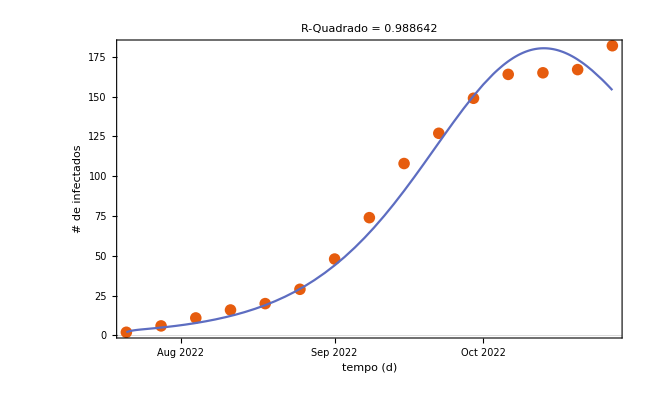

```mathematica
00001.260604874863131`3*10^-4
```

0.000126

```mathematica
RealDigits[0.0001260604874863131`3.]
```

{{1,2,6},-3}

```mathematica
Chunk[list_,chunk_]:=Flatten[Partition[list,chunk][[#;;;;2]]]&/@{1,2}
```

```mathematica
fits ={fitInfectedDynamic, fitInfectedDynamic02, fitInfectedDynamic03, fitInfectedDynamic04}
```

```mathematica
JoinFittedDatePlot[fits_List,fitComplete_FittedModel,{dateMin_DateObject,dateMax_DateObject}]:=
Module[{plotData,bands,cd, chunks},
cd=ColorData[108];
firstFit = First@fits;
lastFit = Last@fits;
plotData=Map[{ToDataDate[dateMin,#1],#2}&@@@#["Data"]&,fits];
bands[x_]=Quiet @ fitComplete["SinglePredictionBands",ConfidenceLevel->0.95]&/. t->x;
Show[DateListPlot[plotData,Joined->True,PlotRange->All],
Plot[{fitComplete[ToModelTime[dateMin,FromAbsoluteTime@t]]&,
bands[ToModelTime[dateMin,FromAbsoluteTime@t]]},
{t,AbsoluteTime@dateMin,AbsoluteTime@dateMax},
PlotRange->All,
PlotStyle->{cd[2],None},
Filling->{2->{1}},
FillingStyle->{Opacity[0.5,Lighter@cd[2]]},
Exclusions->None],
PlotRange->All,
PlotRangePadding->{Automatic,{Scaled[0.03],Scaled[0.1]}},
FrameLabel->{"tempo (d)","# de infectados"},ImageSize->360,
PlotLabel->StringForm["Simulações com parâmetros ajustados"]]
//Labeled[#,Column[{LineLegend[{cd[1]},{"S01"}],LineLegend[{cd[2]},{"S02"}],LineLegend[{cd[3]},{"S03"}],LineLegend[{cd[4]},{"S04"}]},Left],Right]&]
```

FittedModel::precw: The precision of the argument function (MachinePrecision) is less than WorkingPrecision (3).

ParametricNDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

FittedModel::precw: The precision of the argument function (MachinePrecision) is less than WorkingPrecision (3).

ParametricNDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

FittedModel::precw: The precision of the argument function (MachinePrecision) is less than WorkingPrecision (3).

General::stop: Further output of FittedModel::precw will be suppressed during this calculation.

ParametricNDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

General::stop: Further output of ParametricNDSolve::ihist will be suppressed during this calculation.

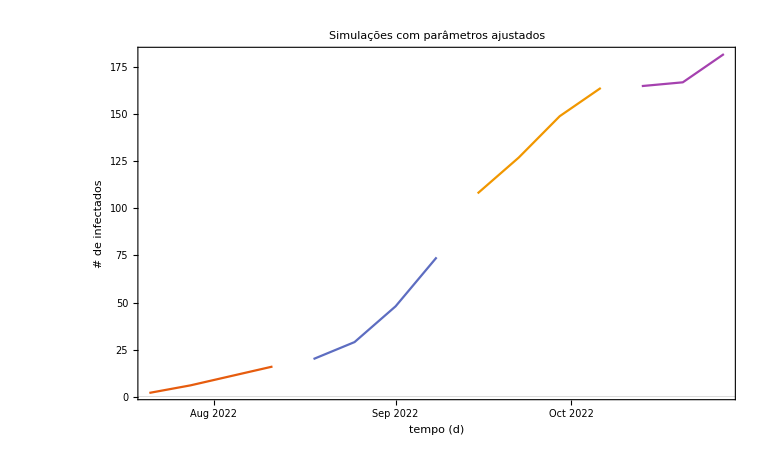

```mathematica
JoinFittedDatePlot[fits,fitInfectedDynamicAll, {First@First@Normal[currentDynamic],First@Last@Normal[currentDynamic]}]
```

```mathematica
dateMin = First@First@Normal[currentDynamic];
dateMax = First@Last@Normal[currentDynamic];
bands[x_,t_]=Quiet @ Map[#["SinglePredictionBands",ConfidenceLevel->0.95]&/. t->x, fits]
```

{{ComplexInfinity √(2.8168+7835.23 (InterpolatingFunction[…][t])^2+417.751 (InterpolatingFunction[…][t])^2+4175.21 InterpolatingFunction[…][t] InterpolatingFunction[…][t]+10434.7 (InterpolatingFunction[…][t])^2+InterpolatingFunction[…][t] (3618.37 InterpolatingFunction[…][t]+18082.7 InterpolatingFunction[…][t]))+InterpolatingFunction[…][t],ComplexInfinity √(2.8168+7835.23 (InterpolatingFunction[…][t])^2+417.751 (InterpolatingFunction[…][t])^2+4175.21 InterpolatingFunction[…][t] InterpolatingFunction[…][t]+10434.7 (InterpolatingFunction[…][t])^2+InterpolatingFunction[…][t] (3618.37 InterpolatingFunction[…][t]+18082.7 InterpolatingFunction[…][t]))+InterpolatingFunction[…][t]},{ComplexInfinity √(3.51693+0.941539 (InterpolatingFunction[…][t])^2+0.426165 (InterpolatingFunction[…][t])^2+InterpolatingFunction[…][t] (1.26333 InterpolatingFunction[…][t]-0.479203 InterpolatingFunction[…][t])-0.337604 InterpolatingFunction[…][t] InterpolatingFunction[…][t]+0.0881674 (InterpolatingFunction[…][t])^2)+InterpolatingFunction[…][t],ComplexInfinity √(3.51693+0.941539 (InterpolatingFunction[…][t])^2+0.426165 (InterpolatingFunction[…][t])^2+InterpolatingFunction[…][t] (1.26333 InterpolatingFunction[…][t]-0.479203 InterpolatingFunction[…][t])-0.337604 InterpolatingFunction[…][t] InterpolatingFunction[…][t]+0.0881674 (InterpolatingFunction[…][t])^2)+InterpolatingFunction[…][t]},{ComplexInfinity √(90.6458+0.572763 (InterpolatingFunction[…][t])^2+0.826596 (InterpolatingFunction[…][t])^2-4.63131 InterpolatingFunction[…][t] InterpolatingFunction[…][t]+6.50531 (InterpolatingFunction[…][t])^2+InterpolatingFunction[…][t] (-1.35813 InterpolatingFunction[…][t]+3.83758 InterpolatingFunction[…][t]))+InterpolatingFunction[…][t],ComplexInfinity √(90.6458+0.572763 (InterpolatingFunction[…][t])^2+0.826596 (InterpolatingFunction[…][t])^2-4.63131 InterpolatingFunction[…][t] InterpolatingFunction[…][t]+6.50531 (InterpolatingFunction[…][t])^2+InterpolatingFunction[…][t] (-1.35813 InterpolatingFunction[…][t]+3.83758 InterpolatingFunction[…][t]))+InterpolatingFunction[…][t]},Missing[]}

```mathematica
plotData=Map[{ToDataDate[dateMin,#1],#2}&@@@#["Data"]&,fits]
```

FittedModel::precw: The precision of the argument function (MachinePrecision) is less than WorkingPrecision (3).

ParametricNDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

FittedModel::precw: The precision of the argument function (MachinePrecision) is less than WorkingPrecision (3).

ParametricNDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

FittedModel::precw: The precision of the argument function (MachinePrecision) is less than WorkingPrecision (3).

General::stop: Further output of FittedModel::precw will be suppressed during this calculation.

ParametricNDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

General::stop: Further output of ParametricNDSolve::ihist will be suppressed during this calculation.

{{{Thu 21 Jul 2022 00:00:00GMT-3,2},{Thu 28 Jul 2022 00:00:00GMT-3,6},{Thu 4 Aug 2022 00:00:00GMT-3,11},{Thu 11 Aug 2022 00:00:00GMT-3,16}},{{Thu 18 Aug 2022 00:00:00GMT-3,20},{Thu 25 Aug 2022 00:00:00GMT-3,29},{Thu 1 Sep 2022 00:00:00GMT-3,48},{Thu 8 Sep 2022 00:00:00GMT-3,74}},{{Thu 15 Sep 2022 00:00:00GMT-3,108},{Thu 22 Sep 2022 00:00:00GMT-3,127},{Thu 29 Sep 2022 00:00:00GMT-3,149},{Thu 6 Oct 2022 00:00:00GMT-3,164}},{{Thu 13 Oct 2022 00:00:00GMT-3,165},{Thu 20 Oct 2022 00:00:00GMT-3,167},{Thu 27 Oct 2022 00:00:00GMT-3,182}}}

InterpolatingFunction::dmval: Input value {3.86735×10^9} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

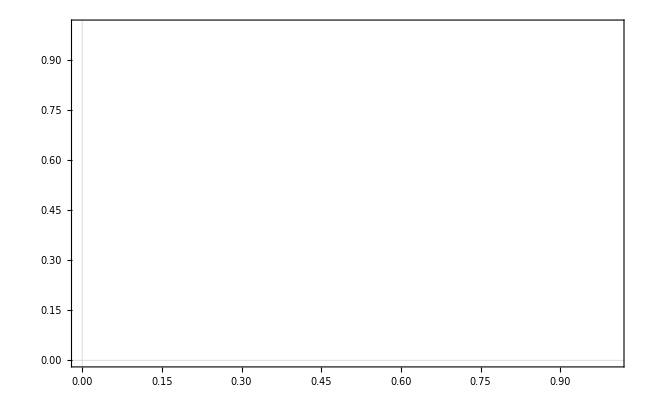

```mathematica
Plot[Map[{#[ToModelTime[dateMin,FromAbsoluteTime@t]]&,
bands[ToModelTime[dateMin,FromAbsoluteTime@t], t]}, fits],
{t,AbsoluteTime@dateMin,AbsoluteTime@dateMax},
PlotRange->All,PlotStyle->{None},Filling->{2->{1}},Exclusions->None]
```